## Definitions

```mathematica
ncdf[z_]:=1/2 Erfc[-z/(√2)];
```

```mathematica
npdf[z_]:=(ⅇ^(-z^2/2))/(√(2 π));
```

```mathematica
Pt[sud_,ud_,s0_,α_,η_,σ_,μ_,t_]:=Module[{ω,x0,b1,b2,yn,zn,n=0,ans=0,ϵ=10^-10,pn=1},
If[t==0,0,
ω=μ-1/2 σ^2;
x0=Log[s0+sud(1/2-η)α];
b1=Log[s0+ud(1/2+η)α];
b2=Log[s0-ud(1/2+η)α];
While[pn>ϵ,
n++;
yn=+ud*(2*(n-1)*b2-(2n-1)*b1+x0);
zn=+ud*(2*n*b2-(2n-1)*b1-x0);
pn=
(ⅇ^(ω/σ^2 yn)ncdf[(yn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 yn)ncdf[(yn-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 zn)ncdf[(zn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 zn)ncdf[(zn-ω t)/(σ √t)]);
ans+=pn;]];
ⅇ^(ω/σ^2(b1-x0))ans];
```

```mathematica
Ptinfmu0[sud_,ud_,s0_,α_,η_,σ_]:=Module[{x0,b1,b2},
x0=Log[s0+sud(1/2-η)α];
b1=Log[s0+ud(1/2+η)α];
b2=Log[s0-ud(1/2+η)α];
ⅇ^((x0-b1)((1+ud)/2)) ((1-ⅇ^(ud(b2-x0)))/(1-ⅇ^(ud(b2-b1))))];
```

```mathematica
Limit[ⅇ^((μ-1/2 σ^2)/σ^2(b1-x0)(1-Sign[μ-1/2 σ^2]ud)) ((1-ⅇ^(2 Abs[μ-1/2 σ^2]/σ^2 ud(b2-x0)))/(1-ⅇ^(2 Abs[μ-1/2 σ^2]/σ^2 ud(b2-b1)))),μ-> 1/2 σ^2]
```

(-b2+x0)/(b1-b2)

```mathematica
Ptinf[sud_,ud_,s0_,α_,η_,σ_,μ_]:=Module[{ω,x0,b1,b2},
ω=μ-1/2 σ^2;
x0=Log[s0+sud(1/2-η)α];
b1=Log[s0+ud(1/2+η)α];
b2=Log[s0-ud(1/2+η)α];
If[ω==0,(b2-x0)/(b2-b1),
ⅇ^(ω/σ^2(b1-x0)(1-Sign[ω]ud)) ((1-ⅇ^(2 Abs[ω]/σ^2 ud(b2-x0)))/(1-ⅇ^(2 Abs[ω]/σ^2 ud(b2-b1))))]];
```

```mathematica
Ptinf4[s0_,α_,η_,σ_,μ_]:=Module[{PAU,PAD,PCU,PCD},
{PAU,PAD,PCU,PCD}={
Ptinf[+1,+1,s0,α,η,σ,μ],Ptinf[-1,-1,s0,α,η,σ,μ],
Ptinf[-1,+1,s0,α,η,σ,μ],Ptinf[+1,-1,s0,α,η,σ,μ]};
{PAU,PAD,PCU,PCD}];
```

```mathematica
Freq4[s0_,α_,η_,σ_,μ_]:=Module[{PAU,PAD,PCU,PCD},
{PAU,PAD,PCU,PCD}={
Ptinf[+1,+1,s0,α,η,σ,μ],Ptinf[-1,-1,s0,α,η,σ,μ],
Ptinf[-1,+1,s0,α,η,σ,μ],Ptinf[+1,-1,s0,α,η,σ,μ]};
{(PAU PAD)/(PAU +PAD),(PAU PAD)/(PAU +PAD),(PAU (1-PAD))/(PAU +PAD),((1-PAU) PAD)/(PAU +PAD)}];
```

```mathematica
FullSimplify[((PAU (1-PAD))/(PAU +PAD)+((1-PAU) PAD)/(PAU +PAD))/(2((PAU PAD)/(PAU +PAD)+(PAU PAD)/(PAU +PAD)))]
```

(PAD+PAU-2 PAD PAU)/(4 PAD PAU)

```mathematica
FullSimplify[Refine[Ptinf4[s0,α,η,σ,0],σ>0]]
```

{1/(1+2 η),1/(1+2 η),(2 η)/(1+2 η),(2 η)/(1+2 η)}

```mathematica
FullSimplify[Refine[Freq4[s0,α,η,σ,0],σ>0]]
```

{1/(2+4 η),1/(2+4 η),η/(1+2 η),η/(1+2 η)}

```mathematica
FullSimplify[Total[ExpandAll[Refine[Ptinf4[s0,α,η,σ,μ],σ>0&&μ>σ^2/2]]]]
```

1

```mathematica
dPt[sud_,ud_,s0_,α_,η_,σ_,μ_,t_,δt_:0.0001]:=(Pt[sud,ud,s0,α,η,σ,μ,t(1+δt)]-Pt[sud,ud,s0,α,η,σ,μ,t(1-δt)])/(2t δt Ptinf[sud,ud,s0,α,η,σ,μ]);
```

```mathematica
nmaxd=2000;
```

```mathematica
Ptn[sud_,ud_,s0_,α_,η_,σ_,μ_,t_, nmax_:nmaxd]:=Module[{ω,x0,b1,b2,yn,zn},
If[t==0,0,
ω=μ-1/2 σ^2;
x0=Log[s0+sud(1/2-η)α];
b1=Log[s0+ud(1/2+η)α];
b2=Log[s0-ud(1/2+η)α];
ⅇ^(ω/σ^2(b1-x0))*Sum[Quiet[
yn=+ud*(2*(n-1)*b2-(2n-1)*b1+x0);
zn=+ud*(2*n*b2-(2n-1)*b1-x0);
(ⅇ^(ω/σ^2 yn)ncdf[(yn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 yn)ncdf[(yn-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 zn)ncdf[(zn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 zn)ncdf[(zn-ω t)/(σ √t)])],{n,1,nmax}]]];
```

```mathematica
tfromp[sud_,ud_,s0_,α_,η_,σ_,μ_,p_,scaled_:True]:=Module[{pmax,τ},
pmax=Pt[sud,ud,s0,α,η,σ,μ,1];
Ptt[t_?NumericQ]:=Pt[sud,ud,s0,α,η,σ,μ,t];
τ=FindRoot[Ptt[t]==p pmax,{t,(η)(α/s0 1/σ)^2}]⟦1,2⟧;
If[scaled,
τ(1/η)(s0/α σ)^2,τ]];
```

```mathematica
Refine[Ptinf[-1,1,s0,α,η,σ,μ],μ>1/2 σ^2]
```

(1-ⅇ^((2 (μ-σ^2/2) (-Log[s0-α (1/2-η)]+Log[s0-α (1/2+η)]))/σ^2))/(1-ⅇ^((2 (μ-σ^2/2) (Log[s0-α (1/2+η)]-Log[s0+α (1/2+η)]))/σ^2))

```mathematica
Refine[Ptinf[-1,1,s0,α,η,σ,μ],μ<1/2 σ^2]
```

(ⅇ^((2 (μ-σ^2/2) (-Log[s0-α (1/2-η)]+Log[s0+α (1/2+η)]))/σ^2) (1-ⅇ^((2 (-μ+σ^2/2) (-Log[s0-α (1/2-η)]+Log[s0-α (1/2+η)]))/σ^2)))/(1-ⅇ^((2 (-μ+σ^2/2) (Log[s0-α (1/2+η)]-Log[s0+α (1/2+η)]))/σ^2))

```mathematica
{ⅇ^(-Log[s0-α (1/2-η)]+Log[s0+α (1/2+η)]) ,ⅇ^(-Log[s0-α (1/2-η)]+Log[s0-α (1/2+η)]),ⅇ^(Log[s0-α (1/2+η)]-Log[s0+α (1/2+η)]),Expand[(2 (μ-σ^2/2))/σ^2],Expand[(2 (-μ+σ^2/2))/σ^2]}
```

{(s0+α (1/2+η))/(s0-α (1/2-η)),(s0-α (1/2+η))/(s0-α (1/2-η)),(s0-α (1/2+η))/(s0+α (1/2+η)),-1+(2 μ)/σ^2,1-(2 μ)/σ^2}

```mathematica
FullSimplify[(s0-α (1/2-η)-(s0-α (1/2+η)))/(s0+α (1/2+η)-(s0-α (1/2+η)))]
```

(2 η)/(1+2 η)

```mathematica
μ=0:((s0+α (1/2+η))/(s0-α (1/2-η)))^-1(1-((s0-α (1/2+η))/(s0-α (1/2-η)))^1)/(1-((s0-α (1/2+η))/(s0+α (1/2+η)))^1)->(s0-α (1/2-η))/(s0+α (1/2+η))(1-(s0-α (1/2+η))/(s0-α (1/2-η)))/(1-(s0-α (1/2+η))/(s0+α (1/2+η)))->(s0-α (1/2-η))/(s0+α (1/2+η))(s0-α (1/2-η)-(s0-α (1/2+η)))/(s0+α (1/2+η)-(s0-α (1/2+η)))(s0+α (1/2+η))/(s0-α (1/2-η))->(2 η)/(1+2 η)
```

```mathematica
μ<1/2 σ^2:((s0+α (1/2+η))/(s0-α (1/2-η)))^(-1+(2 μ)/σ^2)(1-((s0-α (1/2+η))/(s0-α (1/2-η)))^(1-(2 μ)/σ^2))/(1-((s0-α (1/2+η))/(s0+α (1/2+η)))^(1-(2 μ)/σ^2))-> ((s0-α (1/2-η))/(s0+α (1/2+η)))^(1-(2 μ)/σ^2)((s0-α (1/2-η))^(1-(2 μ)/σ^2)-(s0-α (1/2+η))^(1-(2 μ)/σ^2))/((s0+α (1/2+η))^(1-(2 μ)/σ^2)-(s0-α (1/2+η))^(1-(2 μ)/σ^2))((s0+α (1/2+η))/(s0-α (1/2-η)))^(1-(2 μ)/σ^2)-> ((s0-α (1/2-η))^(1-(2 μ)/σ^2)-(s0-α (1/2+η))^(1-(2 μ)/σ^2))/((s0+α (1/2+η))^(1-(2 μ)/σ^2)-(s0-α (1/2+η))^(1-(2 μ)/σ^2))
```

```mathematica
μ>1/2 σ^2:(1-((s0-α (1/2+η))/(s0-α (1/2-η)))^(-1+(2 μ)/σ^2))/(1-((s0-α (1/2+η))/(s0+α (1/2+η)))^(-1+(2 μ)/σ^2))->((s0-α (1/2-η))^(-1+(2 μ)/σ^2)-(s0-α (1/2+η))^(-1+(2 μ)/σ^2))/((s0+α (1/2+η))^(-1+(2 μ)/σ^2)-(s0-α (1/2+η))^(-1+(2 μ)/σ^2)) ((s0+α (1/2+η))/(s0-α (1/2-η)))^(-1+(2 μ)/σ^2)
```

```mathematica
{Ptn[-1,+1,100,0.01,0.5,0.01,1/2 0.01^2,1000,20000],Ptn[-1,-1,100,0.01,0.5,0.01,1/2 0.01^2,1000,20000],
Ptn[+1,+1,100,0.01,0.5,0.01,1/2 0.01^2,1000,20000],Ptn[+1,-1,100,0.01,0.5,0.01,1/2 0.01^2,1000,20000]}
```

{0.500025,0.499975,0.500025,0.499975}

```mathematica
Limit[ncdf[-1/√t],t-> ∞]
```

1/2

```mathematica
∑_(n=1)^∞ (ⅇ^(k y)ⅇ^(k 2(n-1)z))
```

-ⅇ^(k y)/(-1+ⅇ^(2 k z))

```mathematica
{Ptn[-1,+1,100,0.01,0.5,0.01,2 1/2 0.01^2,1000,20000],Ptn[-1,-1,100,0.01,0.5,0.01,2 1/2 0.01^2,1000,20000],
Ptn[+1,+1,100,0.01,0.5,0.01,2 1/2 0.01^2,1000,20000],Ptn[+1,-1,100,0.01,0.5,0.01,2 1/2 0.01^2,1000,20000]}
```

{0.50005,0.49995,0.50005,0.49995}

```mathematica
{Ptn[-1,+1,100,0.01,0.5,0.01,1/2 1/2 0.01^2,1000,20000],Ptn[-1,-1,100,0.01,0.5,0.01,1/2 1/2 0.01^2,1000,20000],
Ptn[+1,+1,100,0.01,0.5,0.01,1/2 1/2 0.01^2,1000,20000],Ptn[+1,-1,100,0.01,0.5,0.01,1/2 1/2 0.01^2,1000,20000]}
```

{0.500013,0.499987,0.500013,0.499987}

```mathematica
{Ptinfmu0[-1,1,100,0.01,0.5,0.01],Ptinfmu0[-1,-1,100,0.01,0.5,0.01],Ptinfmu0[1,1,100,0.01,0.5,0.01],Ptinfmu0[1,-1,100,0.01,0.5,0.01]}
```

{0.5,0.5,0.5,0.5}

```mathematica
{Ptinf[-1,1,100,0.01,0.5,0.01,0],Ptinf[-1,-1,100,0.01,0.5,0.01,0],Ptinf[1,1,100,0.01,0.5,0.01,0],Ptinf[1,-1,100,0.01,0.5,0.01,0]}
```

{0.5,0.5,0.5,0.5}

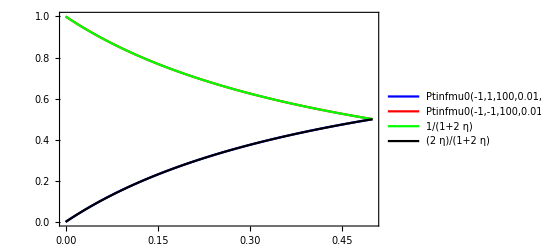

```mathematica
Plot[{Ptinfmu0[-1,1,100,0.01,η,0.01],Ptinfmu0[-1,-1,100,0.01,η,0.01],1/(1+2η),(2η)/(1+2η)},{η,0,1/2},Frame->True,PlotRange->All,PlotStyle->{Blue,Red,Green,Black},PlotLegends->"Expressions"]
```

```mathematica
Plot3D[Ptinf[-1,1,100,0.01,η,0.01,μ],{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

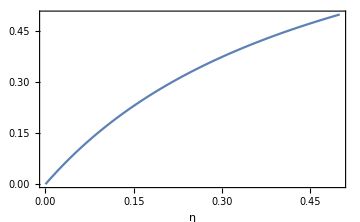

```mathematica
Plot[Ptinf[-1,1,100,0.01,η,0.01,1/2 0.01^2],{η,0,1/2},PlotRange->All,ImageSize->Medium,AxesLabel->Automatic,Frame->True]
```

```mathematica
Plot3D[{Ptinf[-1,1,100,0.01,η,0.01,μ],Ptinf[-1,-1,100,0.01,η,0.01,μ]},{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Ptinf[-1,1,100,0.01,η,0.01,μ]/((2 η)/(1+2 η))-μ,{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

## Approximations

```mathematica
AproxPCoUp[s0_,α_,η_,σ_,μ_]:=(2 η)/(1+2 η)(2/(1+ⅇ^(-2 μ/σ^2*(α/s0))));
```

```mathematica
AproxPCoDown[s0_,α_,η_,σ_,μ_]:=(2 η)/(1+2 η)(2/(1+ⅇ^(2 μ/σ^2*(α/s0))));
```

```mathematica
AproxPAlDown[s0_,α_,η_,σ_,μ_]:=1-(2 η)/(1+2 η)(2/(1+ⅇ^(-2 μ/σ^2*(α/s0))));
```

```mathematica
AproxPAlUp[s0_,α_,η_,σ_,μ_]:=1-(2 η)/(1+2 η)(2/(1+ⅇ^(2 μ/σ^2*(α/s0))));
```

```mathematica
FullSimplify[AproxPAlUp[s0,α,η,σ,μ]AproxPAlDown[s0,α,η,σ,μ]]/FullSimplify[AproxPAlUp[s0,α,η,σ,μ]+AproxPAlDown[s0,α,η,σ,μ]]
```

(1-4 η^2 Tanh[(α μ)/(s0 σ^2)]^2)/(2 (1+2 η))

```mathematica
FullSimplify[AproxPAlUp[s0,α,η,σ,μ]AproxPCoUp[s0,α,η,σ,μ]]/FullSimplify[AproxPAlUp[s0,α,η,σ,μ]+AproxPAlDown[s0,α,η,σ,μ]]
```

(η (1+Tanh[(α μ)/(s0 σ^2)]) (1+2 η Tanh[(α μ)/(s0 σ^2)]))/(1+2 η)

```mathematica
FullSimplify[AproxPAlDown[s0,α,η,σ,μ]AproxPCoDown[s0,α,η,σ,μ]]/FullSimplify[AproxPAlUp[s0,α,η,σ,μ]+AproxPAlDown[s0,α,η,σ,μ]]
```

(2 η (1+ⅇ^((2 α μ)/(s0 σ^2)) (1-2 η)+2 η))/((1+ⅇ^((2 α μ)/(s0 σ^2)))^2 (1+2 η))

```mathematica
FullSimplify[2(1-4 η^2 Tanh[(α μ)/(s0 σ^2)]^2)/(2 (1+2 η))+(η (1+Tanh[(α μ)/(s0 σ^2)]) (1+2 η Tanh[(α μ)/(s0 σ^2)]))/(1+2 η)+(2 η (1+ⅇ^((2 α μ)/(s0 σ^2)) (1-2 η)+2 η))/((1+ⅇ^((2 α μ)/(s0 σ^2)))^2 (1+2 η))]
```

1

```mathematica
FullSimplify[(η (1+Tanh[(α μ)/(s0 σ^2)]) (1+2 η Tanh[(α μ)/(s0 σ^2)]))/(1+2 η)-(2 η (1+ⅇ^((2 α μ)/(s0 σ^2)) (1-2 η)+2 η))/((1+ⅇ^((2 α μ)/(s0 σ^2)))^2 (1+2 η))]
```

2 η Tanh[(α μ)/(s0 σ^2)]

```mathematica
2(1-4 η^2 Tanh[(α μ)/(s0 σ^2)]^2)/(2 (1+2 η))
```

(1-4 η^2 Tanh[(α μ)/(s0 σ^2)]^2)/(1+2 η)

```mathematica
FullSimplify[(2 η)/(1+2 η)(2/(1+ⅇ^(-2 μ/σ^2*(α/s0))))(1-(2 η)/(1+2 η)(2/(1+ⅇ^(2 μ/σ^2*(α/s0)))))-(2 η)/(1+2 η)(2/(1+ⅇ^(2 μ/σ^2*(α/s0))))(1-(2 η)/(1+2 η)(2/(1+ⅇ^(-2 μ/σ^2*(α/s0)))))]
```

(4 η Tanh[(α μ)/(s0 σ^2)])/(1+2 η)

```mathematica
FullSimplify[(1-(2 η)/(1+2 η)(2/(1+ⅇ^(2 μ/σ^2*(α/s0)))))+(1-(2 η)/(1+2 η)(2/(1+ⅇ^(-2 μ/σ^2*(α/s0)))))]
```

2/(1+2 η)

```mathematica
FullSimplify[((4 η Tanh[(α μ)/(s0 σ^2)])/(1+2 η))/(2/(1+2 η))]
```

2 η Tanh[(α μ)/(s0 σ^2)]

```mathematica
Solve[2 η Tanh[(α μ)/(s0 σ^2)]==df,μ]
```

{{μ→ConditionalExpression[(s0 σ^2 (ArcTanh[df/(2 η)]+ⅈ π C[1]))/α, C[1]∈ℤ]}}

```mathematica
Solve[(1-4 η^2 Tanh[(α μ)/(s0 σ^2)]^2)/(1+2 η)==fa,μ]
```

{{μ→ConditionalExpression[(s0 σ^2 (-ArcTanh[(√(1-fa-2 fa η))/(2 η)]+ⅈ π C[1]))/α, C[1]∈ℤ]},{μ→ConditionalExpression[(s0 σ^2 (ArcTanh[(√(1-fa-2 fa η))/(2 η)]+ⅈ π C[1]))/α, C[1]∈ℤ]}}

```mathematica
fupdown[s0_,α_,η_,σ_,μ_]:=2 η Tanh[(α μ)/(s0 σ^2)];
```

```mathematica
Plot3D[{fupdown[100,0.01,0.5,σ,μ],fupdown[100,0.02,0.5,σ,μ]},{σ,0.005,0.02},{μ,-0.5,+0.5},
PlotRange->All,ImageSize->Large,AxesLabel->Automatic,PlotLegends->"Expressions",ViewPoint->{-1.5,-1,0.75},
Boxed->False,AxesEdge->{{1,1},{0,0},{1,0}}]
```

-Graphics3D-

```mathematica
fupdown2[αS_,η_,μσ2_]:=2 η Tanh[αS μσ2];
```

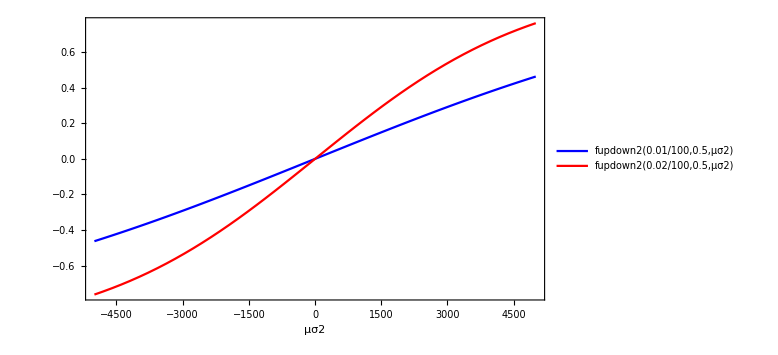

```mathematica
Plot[{fupdown2[0.01/100,0.5,μσ2],fupdown2[0.02/100,0.5,μσ2]},{μσ2,-0.5/0.01^2,+0.5/0.01^2},
PlotRange->All,ImageSize->Large,AxesLabel->Automatic,PlotLegends->"Expressions",Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
Plot3D[{fupdown[100,0.01,η,0.01,μ],fupdown[100,0.02,η,0.01,μ]},{η,0,1/2},{μ,-0.5,+0.5},
PlotRange->All,ImageSize->Large,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
Plot3D[{fupdown[100,0.01,η,0.01,μ],fupdown[100,0.02,η/2,0.01,μ]},{η,0,1/2},{μ,-0.5,+0.5},
PlotRange->All,ImageSize->Large,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
μest[s0_,α_,η_,σ_,df_]:=(s0 σ^2)/α ArcTanh[df/(2 η)];
```

```mathematica
Plot3D[{μest[100,0.01,η,0.01,df],μest[100,0.02,η,0.01,df]},{η,0,2},{df,Max[-1,-η],Min[+1,+η]},
ImageSize->Large,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
Plot3D[{μest[100,0.01,η,0.01,df],μest[100,0.02,η,0.01,df]},{η,0.2,0.5},{df,-η,+η},
ImageSize->Large,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
Plot3D[{μest[100,0.01,η,0.01,df],μest[100,0.02,η/2,0.01,df]},{η,0.2,0.5},{df,-η,+η},
ImageSize->Large,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
Plot3D[{μest[100,0.01,η,0.01,df],μest[100,0.01,η,0.02,df]},{η,0.2,0.5},{df,-η,+η},
ImageSize->Large,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

-Graphics3D-

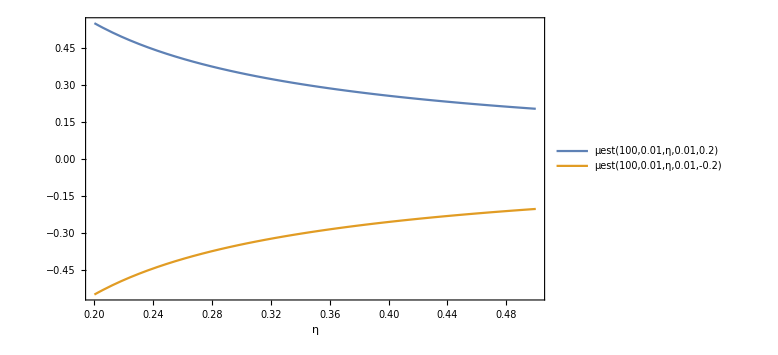

```mathematica
Plot[{μest[100,0.01,η,0.01,0.2],μest[100,0.01,η,0.01,-0.2]},{η,0.2,0.5},
Frame->True,ImageSize->Large,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

```mathematica
Plot3D[{Ptinf[-1,1,100,0.01,η,0.01,μ],AproxPCoUp[100,0.01,η,0.01,μ]},{η,0,1},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{Ptinf[-1,1,100,0.01,η,0.01,μ]-AproxPCoUp[100,0.01,η,0.01,μ],
Ptinf[1,-1,100,0.01,η,0.01,μ]-AproxPCoDown[100,0.01,η,0.01,μ]},{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{Ptinf[-1,1,100,0.01,η,0.01,μ]-Ptinf[1,-1,100,0.01,η,0.01,μ],
AproxPCoUp[100,0.01,η,0.01,μ]-AproxPCoDown[100,0.01,η,0.01,μ]},{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[(AproxPCoUp[100,0.01,η,0.01,μ]-AproxPCoDown[100,0.01,η,0.01,μ])-(Ptinf[-1,1,100,0.01,η,0.01,μ]-Ptinf[1,-1,100,0.01,η,0.01,μ])
,{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[(AproxPCoUp[100,0.01,η,0.01,μ]-AproxPCoDown[100,0.01,η,0.01,μ])/(Ptinf[-1,1,100,0.01,η,0.01,μ]-Ptinf[1,-1,100,0.01,η,0.01,μ]),{η,0,1/2},{μ,-η,+η},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{Ptinf[-1,1,100,0.01,η,0.01,μ],AproxPCoUp[100,0.01,η,0.01,μ]},{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{Ptinf[1,-1,100,0.01,η,0.01,μ],AproxPCoDown[100,0.01,η,0.01,μ]},{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{Ptinf[-1,1,100,0.01,η,0.005,μ],AproxPCoUp[100,0.01,η,0.005,μ]},{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{Ptinf[-1,1,100,0.002,η,0.01,μ],AproxPCoUp[100,0.002,η,0.01,μ]},{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{Ptinf[-1,1,100,0.002,η,0.005,μ],AproxPCoUp[100,0.002,η,0.005,μ]},{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{Ptinf[-1,1,100,α,η,0.01,0],AproxPCoUp[100,α,η,0.01,0]},{η,0,1/2},{α,0.001,0.1},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{Ptinf[-1,1,100,α,η,0.01,0.10],AproxPCoUp[100,α,η,0.01,0.10]},{η,0,1/2},{α,0.001,0.1},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
1-(2 η)/(1+2 η)(1+μ)-> (1+2 η-2 η(1+μ))/(1+2 η)-> (1+2 η-2 η-2 η μ)/(1+2 η)-> (1-2 η μ)/(1+2 η)
```

```mathematica
1-(2 η)/(1+2 η)(1-μ)-> (1+2 η-2 η(1-μ))/(1+2 η)-> (1+2 η-2 η+2 η μ)/(1+2 η)-> (1+2 η μ)/(1+2 η)
```

```mathematica
((1-2 η μ)/(1+2 η)(1+2 η μ)/(1+2 η))/((1-2 η μ)/(1+2 η)+(1+2 η μ)/(1+2 η))-> ((1-2 η μ)/(1+2 η)(1+2 η μ))/(1-2 η μ+1+2 η μ)-> ((1-2 η μ)(1+2 η μ))/(2(1+2 η))-> (1-4 (η μ)^2)/(2(1+2 η))
```

```mathematica
((2 η+2 η μ)/(1+2 η)(1+2 η μ)/(1+2 η))/((1-2 η μ)/(1+2 η)+(1+2 η μ)/(1+2 η))-> ((2 η+2 η μ)/(1+2 η)(1+2 η μ))/(1-2 η μ+1+2 η μ)-> ((2 η+2 η μ)(1+2 η μ))/(2(1+2 η))-> (2 η+2 η^2 μ+2 η μ+4(η μ)^2)/(2(1+2 η))->η (1+η μ+μ+η μ^2)/(1+2 η)->η ((1+η μ)(1+μ))/(1+2 η)
```

```mathematica
((2 η-2 η μ)/(1+2 η)(1-2 η μ)/(1+2 η))/((1-2 η μ)/(1+2 η)+(1+2 η μ)/(1+2 η))-> ((2 η-2 η μ)/(1+2 η)(1-2 η μ))/(1-2 η μ+1+2 η μ)-> ((2 η-2 η μ)(1-2 η μ))/(2(1+2 η))-> (2 η-2 η^2 μ-2 η μ+4(η μ)^2)/(2(1+2 η))->η (1-η μ-μ+η μ^2)/(1+2 η)->η ((1-η μ)(1-μ))/(1+2 η)
```

```mathematica
η ((1+η μ)(1+μ))/(1+2 η)-η ((1-η μ)(1-μ))/(1+2 η)-> η ((1+μ+η μ+η μ^2)-(1-μ-η μ+η μ^2))/(1+2 η)->  μ(2η( 1+η))/(1+2 η)
```

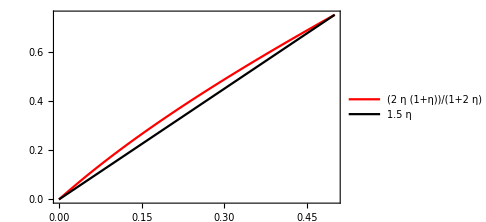

```mathematica
Plot[{(2η( 1+η))/(1+2 η),1.5η},{η,0,1/2},Frame->True,PlotRange->All,ImageSize->Medium,PlotLegends->"Expressions",PlotStyle->{Red,Black}]
```

```mathematica
Plot3D[{Ptinf[-1,-1,100,0.01,η,0.01,μ],(1-2 η μ)/(1+2 η)},{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{Ptinf[1,1,100,0.01,η,0.01,μ],(1+2 η μ)/(1+2 η)},{η,0,1/2},{μ,-0.5,+0.5},PlotRange->All,ImageSize->Large,AxesLabel->Automatic]
```

-Graphics3D-

## Mean conditional durations

E[X]=-∫_(-∞)^0 F[x]ⅆx+∫_0^(+∞) (1-F[x])ⅆx

```mathematica
?ncdf
```

```mathematica
?npdf
```

```mathematica
(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)
```

```mathematica
Integrate[Erfc[t],{t,0,τ}]
```

(ⅇ^(-τ^2) (-1+ⅇ^(τ^2)))/(√π)+τ Erfc[τ]

```mathematica
Integrate[ncdf[t],{t,0,τ}]
```

-1/(√(2 π))+(ⅇ^(-τ^2/2))/(√(2 π))+τ/2+1/2 τ Erf[τ/(√2)]

```mathematica
Integrate[ncdf[y-ω t],{t,0,τ}]
```

(ⅇ^(-y^2/2) √(2/π)-ⅇ^(-1/2 (y-τ ω)^2) √(2/π)+y Erf[y/(√2)]-y Erf[(y-τ ω)/(√2)]+τ ω Erfc[(-y+τ ω)/(√2)])/(2 ω)

```mathematica
inty=FullSimplify[ExpandAll[Integrate[ⅇ^((ω y)/σ^2)ncdf[(y+ω t)/(σ √t)]+ⅇ^(-(ω y)/σ^2)ncdf[(y-ω t)/(σ √t)],{t,0,τ},Assumptions-> y<0&&σ>0&&ω∈Reals]],Assumptions-> y<0&&σ>0&&ω∈Reals]
```

(ⅇ^(-(y ω)/σ^2) (-2 y+ⅇ^((2 y ω)/σ^2) (y+τ ω) (1+Erf[(y+τ ω)/(√2 σ √τ)])+y Erfc[(y-τ ω)/(√2 σ √τ)]+τ ω Erfc[(-y+τ ω)/(√2 σ √τ)]))/(2 ω)

```mathematica
FullSimplify[(ⅇ^(-(y ω)/σ^2) (-2 y+ⅇ^((2 y ω)/σ^2) (y+τ ω) (1+Erf[(y+τ ω)/(√2 σ √τ)])+y Erfc[(y-τ ω)/(√2 σ √τ)]+τ ω Erfc[(-y+τ ω)/(√2 σ √τ)]))/(2 ω)-(+ ⅇ^((y ω)/σ^2)( τ+y/ω)(1 -1/2 Erfc[(y+τ ω)/(√2 σ √τ)])+ ⅇ^(-(y ω)/σ^2) (τ-y/ω)(1-1/2 Erfc[(y-τ ω)/(√2 σ √τ)]))]
```

0

```mathematica
FullSimplify[(ⅇ^(-(y ω)/σ^2) (-2 y+ⅇ^((2 y ω)/σ^2) (y+τ ω) (1+Erf[(y+τ ω)/(√2 σ √τ)])+y Erfc[(y-τ ω)/(√2 σ √τ)]+τ ω Erfc[(-y+τ ω)/(√2 σ √τ)]))/(2 ω)-(+ ⅇ^((y ω)/σ^2)( τ+y/ω)(1 -1/2(2-Erfc[-(y+τ ω)/(√2 σ √τ)]))+ ⅇ^(-(y ω)/σ^2) (τ-y/ω)(1-1/2 (2-Erfc[-(y-τ ω)/(√2 σ √τ)])))]
```

0

```mathematica
FullSimplify[(ⅇ^(-(y ω)/σ^2) (-2 y+ⅇ^((2 y ω)/σ^2) (y+τ ω) (1+Erf[(y+τ ω)/(√2 σ √τ)])+y Erfc[(y-τ ω)/(√2 σ √τ)]+τ ω Erfc[(-y+τ ω)/(√2 σ √τ)]))/(2 ω)-(+ ⅇ^((y ω)/σ^2)( τ+y/ω)(1/2(Erfc[-(y+τ ω)/(√2 σ √τ)]))+ ⅇ^(-(y ω)/σ^2) (τ-y/ω)(1/2 (Erfc[-(y-τ ω)/(√2 σ √τ)])))]
```

0

```mathematica
FullSimplify[(ⅇ^(-(y ω)/σ^2) (-2 y+ⅇ^((2 y ω)/σ^2) (y+τ ω) (1+Erf[(y+τ ω)/(√2 σ √τ)])+y Erfc[(y-τ ω)/(√2 σ √τ)]+τ ω Erfc[(-y+τ ω)/(√2 σ √τ)]))/(2 ω)-(+ ⅇ^((y ω)/σ^2)( τ+y/ω)ncdf[(y+τ ω)/(σ √τ)]+ ⅇ^(-(y ω)/σ^2) (τ-y/ω)ncdf[(y-τ ω)/(σ √τ)])]
```

0

```mathematica
+ ⅇ^((y ω)/σ^2)( τ+y/ω)ncdf[(y+τ ω)/(σ √τ)]+ ⅇ^(-(y ω)/σ^2) (τ-y/ω)ncdf[(y-τ ω)/(σ √τ)]
```

```mathematica
FullSimplify[D[+ ⅇ^((y ω)/σ^2)( τ+y/ω)ncdf[(y+τ ω)/(σ √τ)]+ ⅇ^(-(y ω)/σ^2) (τ-y/ω)ncdf[(y-τ ω)/(σ √τ)],τ]]
```

1/2 ⅇ^(-(y ω)/σ^2) (ⅇ^((2 y ω)/σ^2) (1+Erf[(y+τ ω)/(√2 σ √τ)])+Erfc[(-y+τ ω)/(√2 σ √τ)])

```mathematica
Expand[1/2 ⅇ^(-(y ω)/σ^2) (ⅇ^((2 y ω)/σ^2) (1+1-Erfc[(y+τ ω)/(√2 σ √τ)])+2-Erfc[(y-τ ω)/(√2 σ √τ)])]
```

ⅇ^(-(y ω)/σ^2)+ⅇ^((y ω)/σ^2)-1/2 ⅇ^(-(y ω)/σ^2) Erfc[(y-τ ω)/(√2 σ √τ)]-1/2 ⅇ^((y ω)/σ^2) Erfc[(y+τ ω)/(√2 σ √τ)]

```mathematica
+ⅇ^((y ω)/σ^2)(1-1/2 Erfc[(y+τ ω)/(√2 σ √τ)])+ⅇ^(-(y ω)/σ^2)(1-1/2  Erfc[(y-τ ω)/(√2 σ √τ)])
```

```mathematica
+ⅇ^((y ω)/σ^2)(1-1/2(2-Erfc[-(y+τ ω)/(√2 σ √τ)]))+ⅇ^(-(y ω)/σ^2)(1-1/2  (2-Erfc[-(y-τ ω)/(√2 σ √τ)]))
```

```mathematica
+ⅇ^((y ω)/σ^2)ncdf[(y+τ ω)/(σ √τ)]+ⅇ^(-(y ω)/σ^2)ncdf[(y-τ ω)/(σ √τ)]
```

```mathematica
ⅇ^(ω/σ^2 yn)( yn/ω)-ⅇ^(ω/σ^2 zn)( zn/ω)
```

```mathematica
intPt[sud_,ud_,s0_,α_,η_,σ_,μ_,tmax_,dt_:0.001,all_:True]:=Module[{pinf,scale,tblinterp,trnsp,tblintegr},
pinf=Ptinf[sud,ud,s0,α,η,σ,μ];
scale=(1)(α/s0 1/σ)^2;
tblinterp=Table[{t,dt*(1-Pt[sud,ud,s0,α,η,σ,μ,(t+dt/2)scale]/pinf)},{t,0,tmax-dt,dt}];
trnsp=Transpose[tblinterp];
tblintegr=Transpose[{First[trnsp],Accumulate[Last[trnsp]]}];
If[all,tblintegr,Last[Last[tblintegr]]]];
```

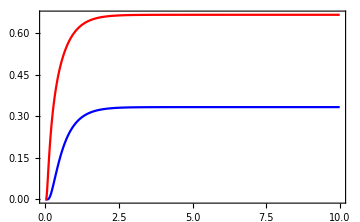

```mathematica
Plot[
{Pt[-1,1,100,0.01,0.25,0.01,0,τ(1)(0.01/100 1/0.01)^2],Pt[-1,-1,100,0.01,0.25,0.01,0,τ(1)(0.01/100 1/0.01)^2]}
,{τ,0,10},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red}]
```

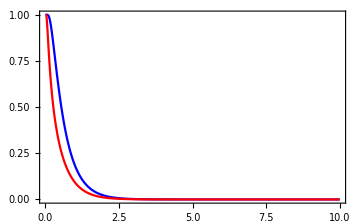

```mathematica
Plot[
{1-Pt[-1,1,100,0.01,0.25,0.01,0,τ(1)(0.01/100 1/0.01)^2]/Ptinf[-1,1,100,0.01,0.25,0.01,0],1-Pt[-1,-1,100,0.01,0.25,0.01,0,τ(1)(0.01/100 1/0.01)^2]/Ptinf[-1,-1,100,0.01,0.25,0.01,0]}
,{τ,0,10},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red}]
```

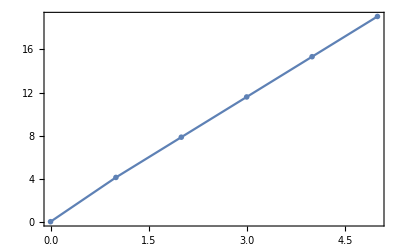

```mathematica
DiscretePlot[tfromp[-1,1,100,0.01,0.5,0.01,0,1-10^-d],{d,0,5},AxesOrigin->{0,0},PlotRange->All,Frame->True,Joined->True,Filling->None,PlotMarkers->"OpenMarkers"]
```

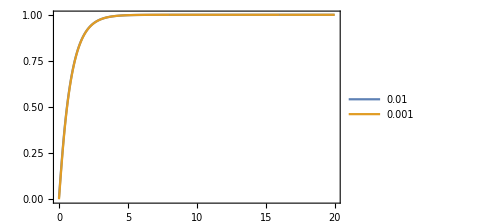

```mathematica
ListPlot[
{intPt[-1,1,100,0.01,0.5,0.01,0,20,0.01,True],
intPt[-1,1,100,0.01,0.5,0.01,0,20,0.001,True]}
,Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,PlotLegends->{0.01,0.001}]
```

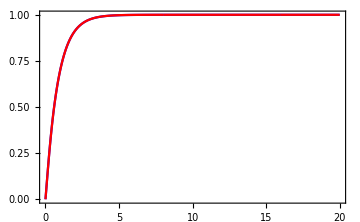

```mathematica
ListPlot[
{intPt[-1,1,100,0.01,0.5,0.01,0,20,0.001,True],
intPt[-1,-1,100,0.01,0.5,0.01,0,20,0.001,True]}
,Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,PlotStyle->{Blue,Red}]
```

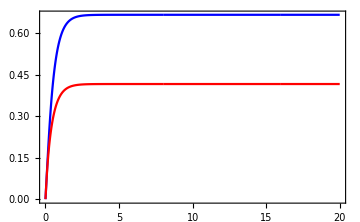

```mathematica
ListPlot[
{intPt[-1,1,100,0.01,0.25,0.01,0,20,0.001,True],
intPt[-1,-1,100,0.01,0.25,0.01,0,20,0.001,True]}
,Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,PlotStyle->{Blue,Red}]
```

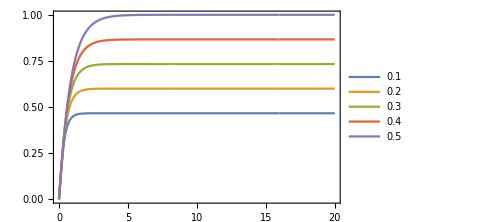

```mathematica
ListPlot[
{intPt[-1,1,100,0.01,0.1,0.01,0,20,0.001,True],
intPt[-1,1,100,0.01,0.2,0.01,0,20,0.001,True],
intPt[-1,1,100,0.01,0.3,0.01,0,20,0.001,True],
intPt[-1,1,100,0.01,0.4,0.01,0,20,0.001,True],
intPt[-1,1,100,0.01,0.5,0.01,0,20,0.001,True]}
,Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,PlotLegends->{0.1,0.2,0.3,0.4,0.5}]
```

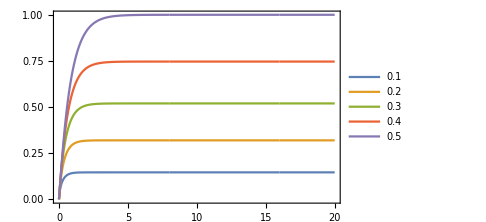

```mathematica
ListPlot[
{intPt[-1,-1,100,0.01,0.1,0.01,0,20,0.001,True],
intPt[-1,-1,100,0.01,0.2,0.01,0,20,0.001,True],
intPt[-1,-1,100,0.01,0.3,0.01,0,20,0.001,True],
intPt[-1,-1,100,0.01,0.4,0.01,0,20,0.001,True],
intPt[-1,-1,100,0.01,0.5,0.01,0,20,0.001,True]}
,Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,PlotLegends->{0.1,0.2,0.3,0.4,0.5}]
```

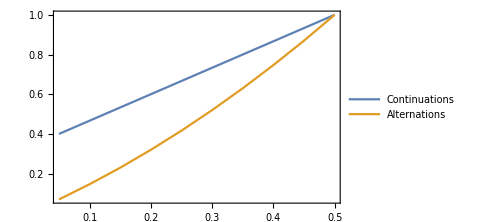

```mathematica
DiscretePlot[
{intPt[-1,1,100,0.01,η,0.01,0,20,0.001,False],
intPt[-1,-1,100,0.01,η,0.01,0,20,0.001,False]},
{η,0.05,0.50,0.05},
Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,PlotLegends->{"Continuations","Alternations"}]
```

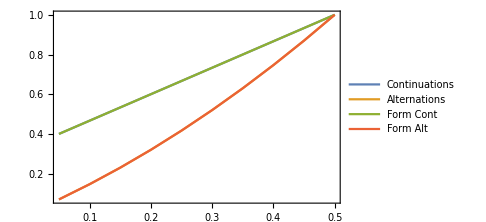

```mathematica
DiscretePlot[
{intPt[-1,1,100,0.01,η,0.01,0,20,0.001,False],
intPt[-1,-1,100,0.01,η,0.01,0,20,0.001,False],
(1+4η)/(6η)2η,(2+2η)/3 2η},
{η,0.05,0.50,0.05},
Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,PlotLegends->{"Continuations","Alternations","Form Cont","Form Alt"}]
```

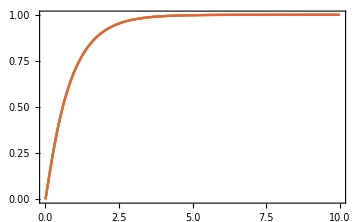

```mathematica
ListPlot[
{intPt[-1,1,100,0.01,0.25,0.01,0,20,0.001,True],
intPt[-1,1,100,0.02,0.25,0.01,0,20,0.001,True],
intPt[-1,1,100,0.01,0.25,0.02,0,20,0.001,True],
intPt[-1,1,100,0.02,0.25,0.02,0,20,0.001,True]}
,Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None]
```

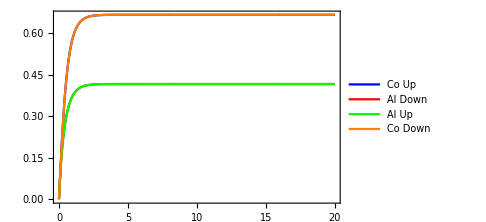

```mathematica
ListPlot[
{intPt[-1,+1,100,0.01,0.25,0.01,0,20,0.001,True],
intPt[-1,-1,100,0.01,0.25,0.01,0,20,0.001,True],
intPt[+1,+1,100,0.01,0.25,0.01,0,20,0.001,True],
intPt[+1,-1,100,0.01,0.25,0.01,0,20,0.001,True]}
,Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,
PlotStyle->{Blue,Red,Green,Orange},
PlotLegends->{"Co Up","Al Down","Al Up","Co Down"}]
```

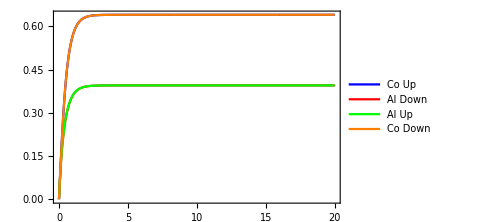

```mathematica
ListPlot[
{intPt[-1,+1,100,0.01,0.25,0.01,0.5,20,0.001,True],
intPt[-1,-1,100,0.01,0.25,0.01,0.5,20,0.001,True],
intPt[+1,+1,100,0.01,0.25,0.01,0.5,20,0.001,True],
intPt[+1,-1,100,0.01,0.25,0.01,0.5,20,0.001,True]}
,Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,
PlotStyle->{Blue,Red,Green,Orange},
PlotLegends->{"Co Up","Al Down","Al Up","Co Down"}]
```

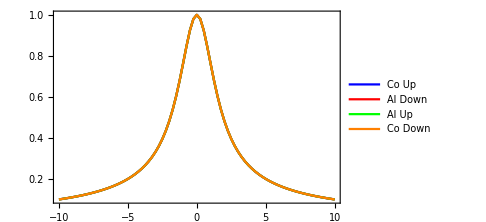

```mathematica
DiscretePlot[
{intPt[-1,+1,100,0.01,0.5,0.01,μ,20,0.01,False],
intPt[-1,-1,100,0.01,0.5,0.01,μ,20,0.01,False],
intPt[+1,+1,100,0.01,0.5,0.01,μ,20,0.01,False],
intPt[+1,-1,100,0.01,0.5,0.01,μ,20,0.01,False]},
{μ,-10.0,+10.0,0.25},
Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,
PlotStyle->{Blue,Red,Green,Orange},
PlotLegends->{"Co Up","Al Down","Al Up","Co Down"}]
```

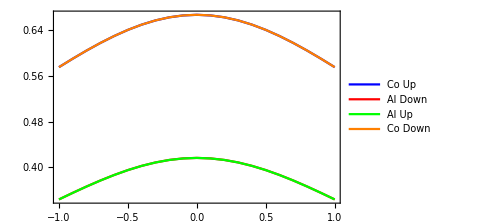

```mathematica
DiscretePlot[
{intPt[-1,+1,100,0.01,0.25,0.01,μ,20,0.01,False],
intPt[-1,-1,100,0.01,0.25,0.01,μ,20,0.01,False],
intPt[+1,+1,100,0.01,0.25,0.01,μ,20,0.01,False],
intPt[+1,-1,100,0.01,0.25,0.01,μ,20,0.01,False]},
{μ,-1.0,+1.0,0.1},
Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,
PlotStyle->{Blue,Red,Green,Orange},
PlotLegends->{"Co Up","Al Down","Al Up","Co Down"}]
```

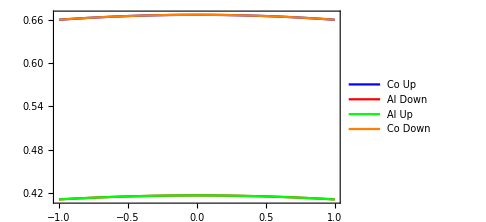

```mathematica
DiscretePlot[
{intPt[-1,+1,100,0.01,0.25,0.02,μ,20,0.01,False],
intPt[-1,-1,100,0.01,0.25,0.02,μ,20,0.01,False],
intPt[+1,+1,100,0.01,0.25,0.02,μ,20,0.01,False],
intPt[+1,-1,100,0.01,0.25,0.02,μ,20,0.01,False]},
{μ,-1.0,+1.0,0.1},
Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,
PlotStyle->{Blue,Red,Green,Orange},
PlotLegends->{"Co Up","Al Down","Al Up","Co Down"}]
```

```mathematica
tau[s0_,α_,η_,σ_,μ_]:=2η(α/(s0 σ))^2;
```

```mathematica
caadj[sud_,ud_,s0_,α_,η_,σ_,μ_]:=If[sud==ud,(2+2η)/3,(1+4η)/(6η)];
```

```mathematica
μadj[s0_,α_,η_,σ_,μ_]:=2/(Exp[μ/(2 σ^2)α/s0]+Exp[-μ/(2 σ^2)α/s0]);
```

```mathematica
μadj2[sud_,ud_,s0_,α_,η_,σ_,μ_]:=1/(1+(μ/(2 √2 σ))^2 (1/σ α/s0)^2);
```

```mathematica
μadj3[s0_,α_,η_,σ_,μ_]:=4 η^2 Sech[(α μ)/(2s0 σ^2)]^2;
```

```mathematica
4 η^2 Sech[(α μ)/(s0 σ^2)]^2
```

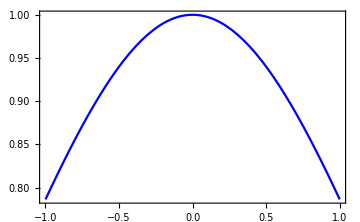

```mathematica
Plot[{μadj3[100,0.01,0.5,0.01,μ]},{μ,-1,+1},Frame->True,PlotRange->All,ImageSize->Medium,PlotStyle->{Blue}]
```

```mathematica
Series[Exp[x],{x,0,3}]
```

1+x+x^2/2+x^3/6+O[x]^4

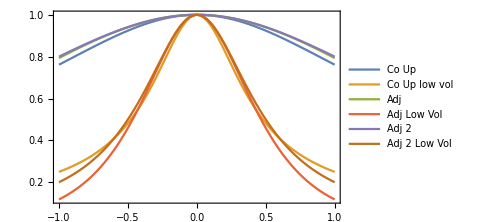

```mathematica
DiscretePlot[
{intPt[-1,+1,100,0.01,0.5,0.01,μ,20,0.1,False],
intPt[-1,+1,100,0.01,0.5,0.005,μ,20,0.1,False],
μadj[100,0.01,0.5,0.01,μ],
μadj[100,0.01,0.5,0.005,μ],
μadj2[100,0.01,0.5,0.01,μ],
μadj2[100,0.01,0.5,0.005,μ]},
{μ,-1.0,+1.0,0.025},
Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,
PlotLegends->{"Co Up","Co Up low vol","Adj","Adj Low Vol","Adj 2","Adj 2 Low Vol"}]
```

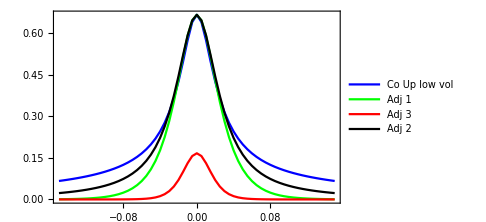

```mathematica
DiscretePlot[
{intPt[-1,+1,100,0.01,0.25,0.001,μ,20,0.01,False],
caadj[-1,+1,100,0.01,0.25,0.001,μ]2 0.25μadj[100,0.01,0.25,0.001,μ],
caadj[-1,+1,100,0.01,0.25,0.001,μ]2 0.25μadj3[100,0.01,0.25,0.001,μ],
caadj[-1,+1,100,0.01,0.25,0.001,μ]2 0.25 μadj2[-1,+1,100,0.01,0.25,0.001,μ]},
{μ,-0.15,+0.15,0.005},
Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,
PlotStyle->{Blue,Green,Red,Black},
PlotLegends->{"Co Up low vol","Adj 1","Adj 3","Adj 2"}]
```

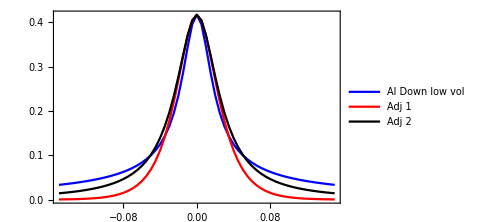

```mathematica
DiscretePlot[
{intPt[-1,-1,100,0.01,0.25,0.001,μ,20,0.01,False],
caadj[-1,-1,100,0.01,0.25,0.001,μ]2 0.25 μadj[100,0.01,0.25,0.001,μ],
caadj[-1,-1,100,0.01,0.25,0.001,μ]2 0.25 μadj2[-1,-1,100,0.01,0.25,0.001,μ]},
{μ,-0.15,+0.15,0.005},
Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,
PlotStyle->{Blue,Red,Black},
PlotLegends->{"Al Down low vol","Adj 1","Adj 2"}]
```

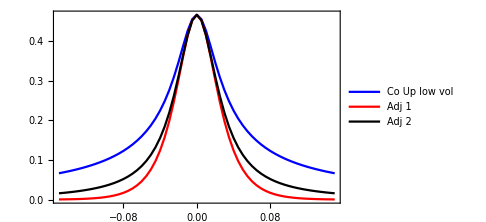

```mathematica
DiscretePlot[
{intPt[-1,+1,100,0.01,0.10,0.001,μ,20,0.01,False],
caadj[-1,+1,100,0.01,0.10,0.001,μ]2 0.10 μadj[100,0.01,0.10,0.001,μ],
caadj[-1,+1,100,0.01,0.10,0.001,μ]2 0.10 μadj2[-1,+1,100,0.01,0.10,0.001,μ]},
{μ,-0.15,+0.15,0.005},
Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,
PlotStyle->{Blue,Red,Black},
PlotLegends->{"Co Up low vol","Adj 1","Adj 2"}]
```

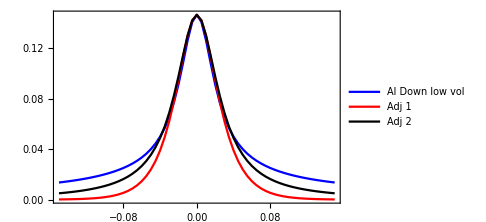

```mathematica
DiscretePlot[
{intPt[-1,-1,100,0.01,0.10,0.001,μ,20,0.01,False],
caadj[-1,-1,100,0.01,0.10,0.001,μ]2 0.10 μadj[100,0.01,0.10,0.001,μ],
caadj[-1,-1,100,0.01,0.10,0.001,μ]2 0.10 μadj2[-1,-1,100,0.01,0.10,0.001,μ]},
{μ,-0.15,+0.15,0.005},
Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,
PlotStyle->{Blue,Red,Black},
PlotLegends->{"Al Down low vol","Adj 1","Adj 2"}]
```

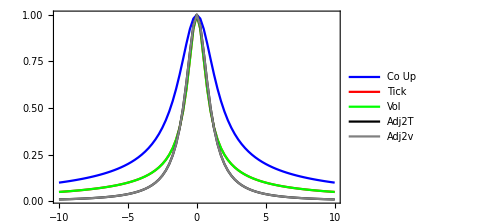

```mathematica
DiscretePlot[
{intPt[-1,+1,100,0.01,0.5,0.01,μ,20,0.01,False],
intPt[-1,+1,100,0.01 2,0.5,0.01,μ,20,0.01,False],
intPt[-1,+1,100,0.01,0.5,0.01/(√2),μ,20,0.01,False],
μadj2[100,0.02,0.5,0.01,μ],
μadj2[100,0.01,0.5,0.01/(√2),μ]},
{μ,-10.0,+10.0,0.25},
Frame->True,PlotRange->All,ImageSize->Medium,
Joined->True,Filling->None,
PlotStyle->{Blue,Red,Green,Black,Gray},
PlotLegends->{"Co Up","Tick","Vol","Adj2T","Adj2v"}]
```

```mathematica
Grid[Table[{σ,tau[-1,1,100,0.01,0.5,σ,0]*9*3600},{σ,{0.001,0.002,0.005,0.01,0.02,0.05,0.1,0.2}}]]
```

0.001 | 324.
0.002 | 81.
0.005 | 12.96
0.01 | 3.24
0.02 | 0.81
0.05 | 0.1296
0.1 | 0.0324
0.2 | 0.0081

```mathematica
{Pt[-1,1,100,0.01,0.25,0.01,0,tau[-1,1,100,0.01,0.25,0.01,0]],
Pt[-1,-1,100,0.01,0.25,0.01,0,tau[-1,-1,100,0.01,0.25,0.01,0]]}
```

{0.152625,0.479084}

```mathematica
{tauca[-1,1,100,0.01,0.25,0.01,0],tauca[-1,-1,100,0.01,0.25,0.01,0]}*9*3600
```

{2.16,1.35}

```mathematica
{Pt[-1,1,100,0.01,0.25,0.01,0,tauca[-1,1,100,0.01,0.25,0.01,0]],
Pt[-1,-1,100,0.01,0.25,0.01,0,tauca[-1,-1,100,0.01,0.25,0.01,0]]}
```

{0.206369,0.438459}

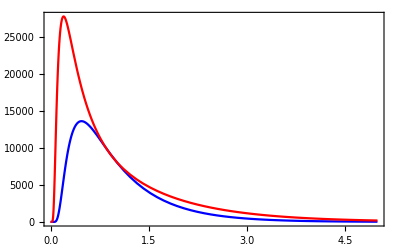

```mathematica
Plot[{
dPt[-1,1,100,0.01,0.25,0.01,0,t tauca[-1,1,100,0.01,0.25,0.01,0]],
dPt[-1,-1,100,0.01,0.25,0.01,0,t tauca[-1,-1,100,0.01,0.25,0.01,0]]},
{t,0,5},Frame->True,PlotRange->All,PlotStyle->{Blue,Red}]
```

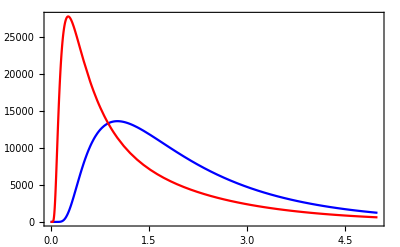

```mathematica
Plot[{
dPt[-1,1,100,0.01,0.25,0.01,0,t/(9*3600)],
dPt[-1,-1,100,0.01,0.25,0.01,0,t/(9*3600)]},
{t,0,5},Frame->True,PlotRange->All,PlotStyle->{Blue,Red}]
```

```mathematica
{Pt[-1,1,100,0.01,0.25,0.01,0,0.01/(9*3600)],Pt[-1,-1,100,0.01,0.25,0.01,0,0.01/(9*3600)]}
```

{1.96398×10^-72,2.248×10^-19}

```mathematica
{Pt[-1,1,100,0.01,0.25,0.02,0,0.015/(9*3600)],Pt[-1,-1,100,0.01,0.25,0.02,0,0.015/(9*3600)]}
```

{2.00755×10^-13,0.000238398}

```mathematica
{Pt[-1,1,100,0.01,0.25,0.1,0,0.01/(9*3600)],Pt[-1,-1,100,0.01,0.25,0.1,0,0.01/(9*3600)]}
```

{0.071546,0.368099}

## Invariances

## μ = 0

### Changes in relative tick

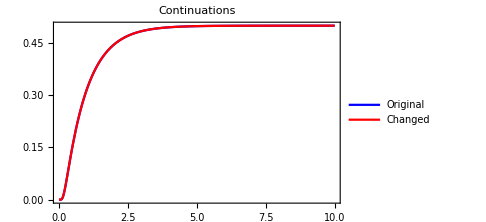
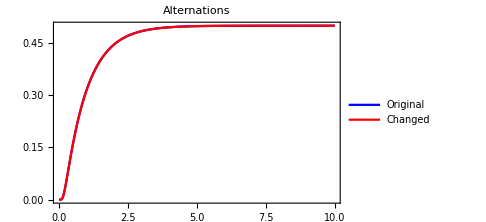
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{Plot[
{+Pt[-1,1,100,0.01,0.5,0.01,0,t (1)(0.01/100 1/0.01)^2],
+Pt[-1,1,100,0.02,0.5,0.01,0,t (1)(0.02/100 1/0.01)^2]},
{t,0,10},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red},PlotLabel->"Continuations",PlotLegends->{"Original", "Changed"}],
Plot[
{+Pt[-1,-1,100,0.01,0.5,0.01,0,t (1)(0.01/100 1/0.01)^2],
+Pt[-1,-1,100,0.02,0.5,0.01,0,t(1)(0.02/100 1/0.01)^2]},
{t,0,10},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red},PlotLabel->"Alternations",PlotLegends->{"Original", "Changed"}]},
{Plot[
{+Pt[-1,1,100,0.01,0.5,0.01,0,t(1)(0.01/100 1/0.01)^2],
+Pt[-1,1,50,0.01,0.5,0.01,0,t(1)(0.01/50 1/0.01)^2]},
{t,0,10},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red},PlotLabel->"Continuations",PlotLegends->{"Original", "Changed"}],
Plot[
{+Pt[-1,-1,100,0.01,0.5,0.01,0,t(1)(0.01/100 1/0.01)^2],
+Pt[-1,-1,50,0.01,0.5,0.01,0,t(1)(0.01/50 1/0.01)^2]},
{t,0,10},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red},PlotLabel->"Alternations",PlotLegends->{"Original", "Changed"}]}}]
```

### Changes in vol

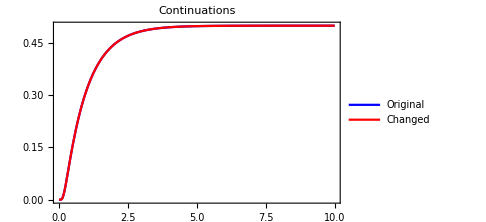
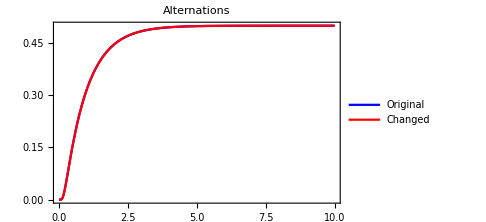
-Graphics- | -Graphics-

```mathematica
Grid[{{Plot[
{+Pt[-1,1,100,0.01,0.5,0.01,0,t(1)(0.01/100 1/0.01)^2],
+Pt[-1,1,100,0.01,0.5,0.02,0,t(1)(0.01/100 1/0.02)^2]},
{t,0,10},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red},PlotLabel->"Continuations",PlotLegends->{"Original", "Changed"}],
Plot[
{+Pt[-1,-1,100,0.01,0.5,0.01,0,t(1)(0.01/100 1/0.01)^2],
+Pt[-1,-1,100,0.01,0.5,0.02,0,t(1)(0.01/100 1/0.02)^2]},
{t,0,10},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red},PlotLabel->"Alternations",PlotLegends->{"Original", "Changed"}]}}]
```

### Changes in eta

```mathematica
0.5 -> 0.25
```

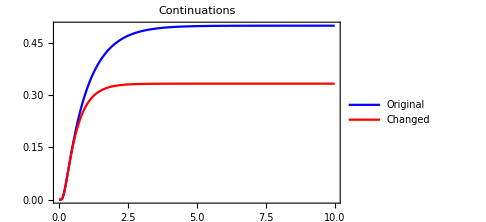
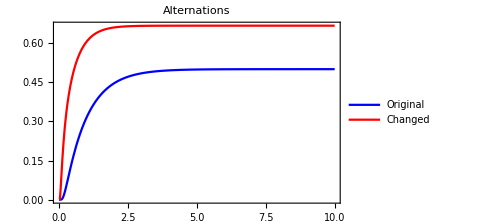
-Graphics- | -Graphics-

```mathematica
Grid[{{Plot[
{+Pt[-1,1,100,0.01,0.5,0.01,0,t(1)(0.01/100 1/0.01)^2],
+Pt[-1,1,100,0.01,0.25,0.01,0,t(1)(0.01/100 1/0.01)^2]},
{t,0,10},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red},PlotLabel->"Continuations",PlotLegends->{"Original", "Changed"}],
Plot[
{+Pt[-1,-1,100,0.01,0.5,0.01,0,t(1)(0.01/100 1/0.01)^2],
+Pt[-1,-1,100,0.01,0.25,0.01,0,t(1)(0.01/100 1/0.01)^2]},
{t,0,10},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red},PlotLabel->"Alternations",PlotLegends->{"Original", "Changed"}]}}]
```

```mathematica
{(2 0.5)/(1+2 0.5),1/(1+2 0.5)}
```

{0.5,0.5}

```mathematica
{(2 0.25)/(1+2 0.25),1/(1+2 0.25)}
```

{0.333333,0.666667}

```mathematica
{(2 0.5)/(1+2 0.5),1/(1+2 0.5)}/{(2 0.25)/(1+2 0.25),1/(1+2 0.25)}
```

{1.5,0.75}

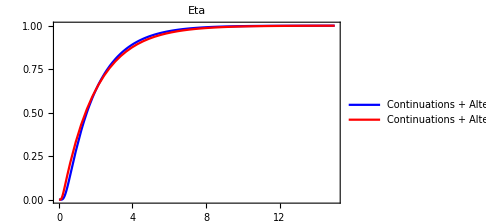

```mathematica
Plot[
{+(1)Pt[-1,1,100,0.01,0.5,0.01,0,t(0.5)(0.01/100 1/0.01)^2]+
+(1)Pt[-1,-1,100,0.01,0.5,0.01,0,t(0.5)(0.01/100 1/0.01)^2],
+(1)Pt[-1,1,100,0.01,0.25,0.01,0,t(0.25)(0.01/100 1/0.01)^2]+
+(1)Pt[-1,-1,100,0.01,0.25,0.01,0,t(0.25)(0.01/100 1/0.01)^2]},
{t,0,15},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red},PlotLabel->"Eta",
PlotLegends->{"Continuations + Alternations Original", "Continuations + Alternations Changed"}]
```

Same scale!

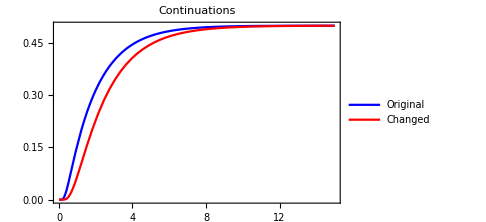
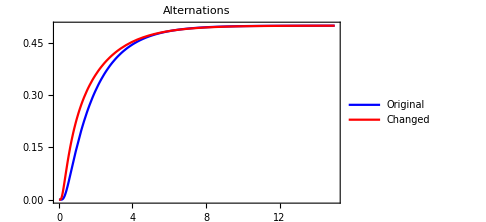
-Graphics- | -Graphics-

```mathematica
Grid[{{Plot[
{+Pt[-1,1,100,0.01,0.5,0.01,0,t(0.5)(0.01/100 1/0.01)^2],
+(((2 0.5)/(1+2 0.5))/((2 0.25)/(1+2 0.25)))Pt[-1,1,100,0.01,0.25,0.01,0,t(0.25)(0.01/100 1/0.01)^2]},
{t,0,15},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red},PlotLabel->"Continuations",PlotLegends->{"Original", "Changed"}],
Plot[
{+Pt[-1,-1,100,0.01,0.5,0.01,0,t(0.5)(0.01/100 1/0.01)^2],
+((1/(1+2 0.5))/(1/(1+2 0.25)))Pt[-1,-1,100,0.01,0.25,0.01,0,t(0.25)(0.01/100 1/0.01)^2]},
{t,0,15},Frame->True,PlotRange->All,ImageSize->Medium,
PlotStyle->{Blue,Red},PlotLabel->"Alternations",PlotLegends->{"Original", "Changed"}]}}]
```

## GIG Fit

```mathematica
PDF[InverseGaussianDistribution[μ,λ],x]
```

Piecewise[{{(ⅇ^(-(λ (x-μ)^2)/(2 x μ^2)) √(λ/x^3))/(√(2 π)), x>0}, {0, True}}]

```mathematica
CDF[InverseGaussianDistribution[μ,λ],x]
```

Piecewise[{{1/2 Erfc[(√(λ/x) (-x+μ))/(√2 μ)]+1/2 ⅇ^((2 λ)/μ) Erfc[(√(λ/x) (x+μ))/(√2 μ)], x>0}, {0, True}}]

```mathematica
Refine[CDF[InverseGaussianDistribution[μ,λ],x],x>0]
```

1/2 Erfc[(√λ (-x+μ))/(√2 √x μ)]+1/2 ⅇ^((2 λ)/μ) Erfc[(√λ (x+μ))/(√2 √x μ)]

```mathematica
1/2 Erfc[(√λ (-x+μ))/(√2 √x μ)]+1/2 ⅇ^((2 λ)/μ) Erfc[(√λ (x+μ))/(√2 √x μ)]
```

```mathematica
ncdf[(-μ √λ +√λ x)/(μ √x)]+ ⅇ^((2 λ)/μ) ncdf[(-μ √λ -√λ x)/(μ √x)]
```

```mathematica
fncdf[μ_,λ_,x_]:=ncdf[(-μ √λ +√λ x)/(μ √x)]+ ⅇ^((2 λ)/μ) ncdf[(-μ √λ -√λ x)/(μ √x)];
```

General::munfl: Exp[-7346.18] is too small to represent as a normalized machine number; precision may be lost.

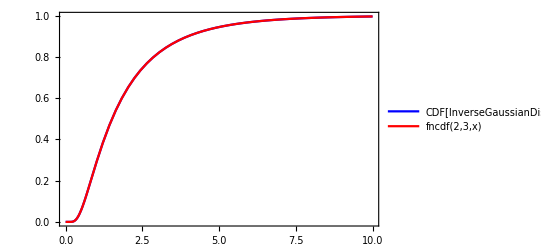

```mathematica
Plot[{CDF[InverseGaussianDistribution[2,3],x],fncdf[2,3,x]},{x,0,10},PlotRange->All,Frame->True,PlotStyle->{Blue,Red},PlotLegends->"Expressions"]
```

```mathematica
Mean[InverseGaussianDistribution[μ,λ]]
```

μ

```mathematica
FullSimplify[Refine[PDF[InverseGaussianDistribution[μ,λ,-1/2],x],x>0&&μ>0]]
```

(ⅇ^(-(λ (x-μ)^2)/(2 x μ^2)) √λ)/(√(2 π) x^(3/2))

```mathematica
FullSimplify[Refine[PDF[InverseGaussianDistribution[μ,λ],x],x>0&&μ>0]]
```

(ⅇ^(-(λ (x-μ)^2)/(2 x μ^2)) √λ)/(√(2 π) x^(3/2))

```mathematica
PDF[InverseGaussianDistribution[μ,λ,θ],x]
```

Piecewise[{{(ⅇ^(-(λ (1+x^2/μ^2))/(2 x)) x^(-1+θ) μ^-θ)/(2 BesselK[θ,λ/μ]), x>0}, {0, True}}]

```mathematica
Refine[PDF[InverseGaussianDistribution[μ,λ,θ],x],x>0]
```

(ⅇ^(-(λ (1+x^2/μ^2))/(2 x)) x^(-1+θ) μ^-θ)/(2 BesselK[θ,λ/μ])

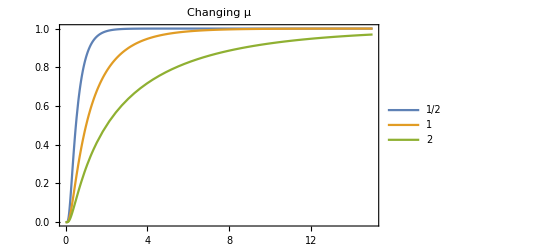

```mathematica
μrng={1/2,1,2};Plot[Table[CDF[InverseGaussianDistribution[μ,1,0],x],{μ,μrng}]//Evaluate,{x,0,15},PlotRange->All,Frame->True,PlotLabel->"Changing μ",PlotLegends->μrng]
```

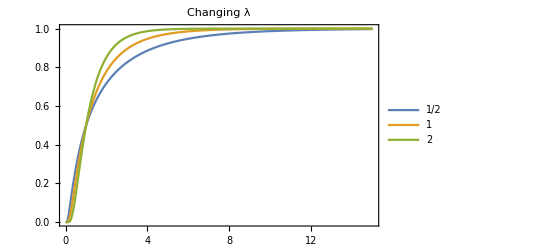

```mathematica
λrng={1/2,1,2};Plot[Table[CDF[InverseGaussianDistribution[1,λ,0],x],{λ,λrng}]//Evaluate,{x,0,15},PlotRange->All,Frame->True,PlotLabel->"Changing λ",PlotLegends->λrng]
```

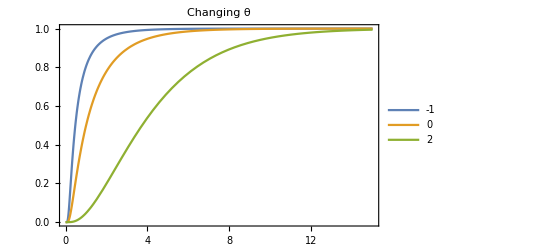

```mathematica
θrng={-1,0,2};Plot[Table[CDF[InverseGaussianDistribution[1,1,θ],x],{θ,θrng}]//Evaluate,{x,0,15},PlotRange->All,Frame->True,PlotLabel->"Changing θ",PlotLegends->θrng]
```

```mathematica
Mean[InverseGaussianDistribution[μ,λ,θ]]
```

(μ BesselK[1+θ,λ/μ])/BesselK[θ,λ/μ]

```mathematica
Variance[InverseGaussianDistribution[μ,λ,θ]]
```

(μ^2 (-BesselK[1+θ,λ/μ]^2+BesselK[θ,λ/μ] BesselK[2+θ,λ/μ]))/BesselK[θ,λ/μ]^2

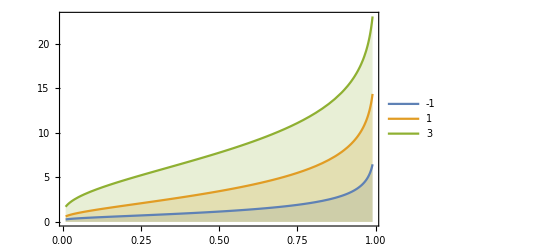

```mathematica
Plot[Table[Quantile[InverseGaussianDistribution[2,3,θ],q],{θ,{-1,1,3}}]//Evaluate,{q,0.01,0.99},Filling->Axis,Frame->True,PlotLegends->{-1,1,3}]
```

```mathematica
{tfromp[-1,1,100,0.01,0.5,0.01,0,0.2],tfromp[-1,1,100,0.01,0.5,0.01,0,0.2,False]}
```

{0.739174,0.0000369587}

```mathematica
rndsmpl=RandomReal[1,100000];
```

```mathematica
iterfit[s0_,α_,η0_,σ0_,μ0_,randomsample_,nmax_,step_]:=
Module[
{ptsCoUp={},ptsAlDown={},ptsAlUp={},ptsCoDown={},
funcs={},j,p,newrow},
For[
j=1,j≤nmax,j++,
p=randomsample⟦j⟧;
ptsCoUp=Append[ptsCoUp,tfromp[-1,1,s0,α,η0,σ0,μ0,p]];
ptsCoDown=Append[ptsCoDown,tfromp[1,-1,s0,α,η0,σ0,μ0,p]];
ptsAlUp=Append[ptsAlUp,tfromp[1,1,s0,α,η0,σ0,μ0,p]];
ptsAlDown=Append[ptsAlDown,tfromp[-1,-1,s0,α,η0,σ0,μ0,p]];
If[Mod[j,step]==0,
newrow=Prepend[Join[
Apply[List,EstimatedDistribution[ptsCoUp,InverseGaussianDistribution[μ,λ,θ]]],
Apply[List,EstimatedDistribution[ptsCoDown,InverseGaussianDistribution[μ,λ,θ]]],
Apply[List,EstimatedDistribution[ptsAlUp,InverseGaussianDistribution[μ,λ,θ]]],
Apply[List,EstimatedDistribution[ptsAlDown,InverseGaussianDistribution[μ,λ,θ]]]
],j];
Print[newrow];
funcs=Append[funcs,newrow]];];
funcs];
```

```mathematica
Grid[iterfit[100,0.01,0.5,0.01,0,rndsmpl,10000,5000]]
```

{5000,1.31995,1.58926,0.203739,1.32007,1.58962,0.20377,1.31995,1.58926,0.203739,1.32007,1.58962,0.20377}

{10000,1.30939,1.59011,0.232452,1.30951,1.59046,0.232486,1.30939,1.59011,0.232452,1.30951,1.59046,0.232486}

5000 | 1.31995 | 1.58926 | 0.203739 | 1.32007 | 1.58962 | 0.20377 | 1.31995 | 1.58926 | 0.203739 | 1.32007 | 1.58962 | 0.20377
10000 | 1.30939 | 1.59011 | 0.232452 | 1.30951 | 1.59046 | 0.232486 | 1.30939 | 1.59011 | 0.232452 | 1.30951 | 1.59046 | 0.232486

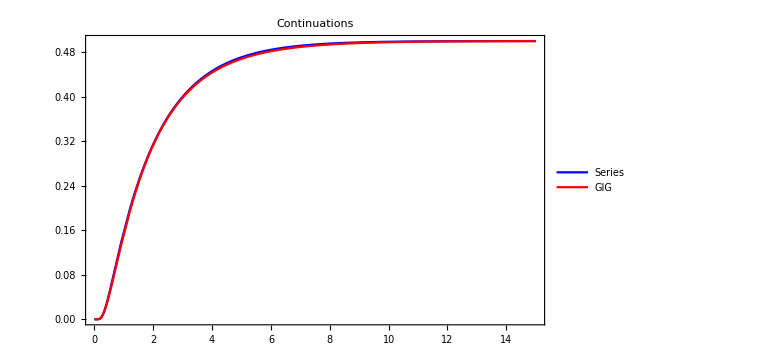
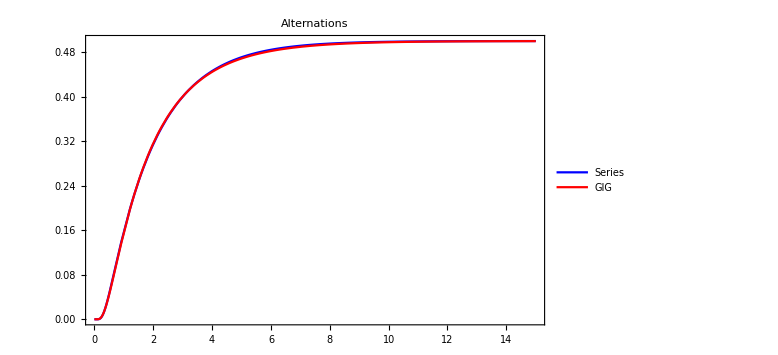

```mathematica
Grid[{{Plot[
{+Pt[-1,1,100,0.01,0.5,0.01,0,t(0.5)(0.01/100 1/0.01)^2],
((2 0.5)/(1+2 0.5))CDF[InverseGaussianDistribution[1.31,1.59,0.23],t]},
{t,0,15},Frame->True,PlotRange->All,ImageSize->Large,
PlotStyle->{Blue,Red},PlotLabel->"Continuations",PlotLegends->{"Series", "GIG"}]},
{Plot[
{+Pt[-1,-1,100,0.01,0.5,0.01,0,t(0.5)(0.01/100 1/0.01)^2],
(1/(1+2 0.5))CDF[InverseGaussianDistribution[1.32,1.60,0.2],t]},
{t,0,15},Frame->True,PlotRange->All,ImageSize->Large,
PlotStyle->{Blue,Red},PlotLabel->"Alternations",PlotLegends->{"Series", "GIG"}]}}]
```

General::munfl: Exp[-2594.41] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2610.72] is too small to represent as a normalized machine number; precision may be lost.

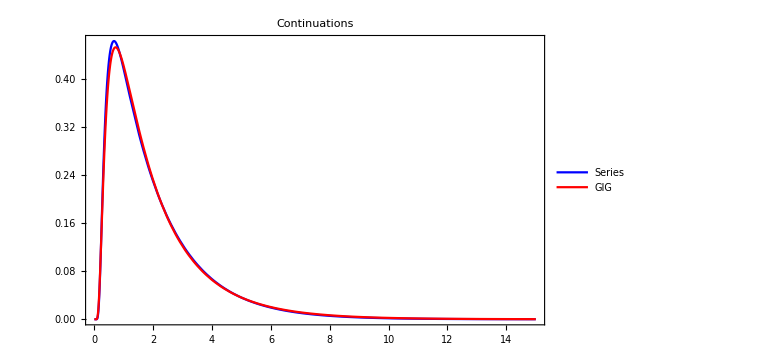
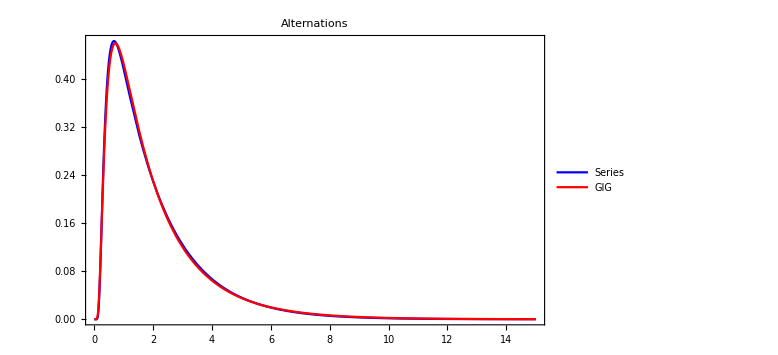

```mathematica
Grid[{{Plot[
{+(0.5)(0.01/100 1/0.01)^2 dPt[-1,1,100,0.01,0.5,0.01,0,t(0.5)(0.01/100 1/0.01)^2],
PDF[InverseGaussianDistribution[1.31,1.59,0.23],t]},
{t,0,15},Frame->True,PlotRange->All,ImageSize->Large,
PlotStyle->{Blue,Red},PlotLabel->"Continuations",PlotLegends->{"Series", "GIG"}]},
{Plot[
{+(0.5)(0.01/100 1/0.01)^2 dPt[-1,-1,100,0.01,0.5,0.01,0,t(0.5)(0.01/100 1/0.01)^2],
PDF[InverseGaussianDistribution[1.32,1.60,0.2],t]},
{t,0,15},Frame->True,PlotRange->All,ImageSize->Large,
PlotStyle->{Blue,Red},PlotLabel->"Alternations",PlotLegends->{"Series", "GIG"}]}}]
```

```mathematica
Grid[iterfit[100,0.01,0.25,0.01,0,rndsmpl,50000,5000]]
```

Greater::nord: Invalid comparison with -1.05757×10^30-1.72714×10^46 ⅈ attempted.

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {3.19041×10^-9}. Try perturbing the initial point(s).

Greater::nord: Invalid comparison with -1.26253×10^30-2.06187×10^46 ⅈ attempted.

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {6.69101×10^-9}. Try perturbing the initial point(s).

Greater::nord: Invalid comparison with -19.5529-3.19323×10^17 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {2.59713×10^-7}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5000,2.06353,3.63955,0.0950527,2.06368,3.64004,0.0949815,0.0121284,0.000187093,1.08105,0.0123462,0.000191652,1.07239}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

{10000,2.04716,3.64359,0.129879,2.0473,3.64408,0.129808,0.00842166,0.0000918911,1.11035,0.0119348,0.000183773,1.10781}

{15000,1.92232,3.43082,0.253467,1.92245,3.43128,0.253406,0.0115899,0.000175144,1.10068,0.0119857,0.000187407,1.10131}

{20000,1.90534,3.42606,0.270499,1.90547,3.42652,0.270438,0.0115537,0.000176306,1.10881,0.0122457,0.000198285,1.11015}

{25000,1.89898,3.38782,0.27149,1.89911,3.38828,0.27143,0.0117466,0.000181424,1.10333,0.0124796,0.000205035,1.10483}

{30000,1.90831,3.40221,0.262816,1.90845,3.40267,0.262755,0.0117382,0.000180077,1.0987,0.0122941,0.000197736,1.09987}

{35000,1.91073,3.43128,0.256668,1.91087,3.43174,0.256606,0.0117222,0.000181578,1.10516,0.0122919,0.000199871,1.10641}

{40000,1.93805,3.48145,0.224738,1.93819,3.48192,0.224674,0.0113174,0.000168866,1.10315,0.0122236,0.000197253,1.10467}

{45000,1.93926,3.46928,0.219709,1.93939,3.46975,0.219646,0.0115097,0.000174288,1.10044,0.0118713,0.00018556,1.10139}

{50000,1.93097,3.45302,0.230649,1.93111,3.45349,0.230584,0.0115685,0.000176419,1.10355,0.0119092,0.000187091,1.10439}

5000 | 2.06353 | 3.63955 | 0.0950527 | 2.06368 | 3.64004 | 0.0949815 | 0.0121284 | 0.000187093 | 1.08105 | 0.0123462 | 0.000191652 | 1.07239
10000 | 2.04716 | 3.64359 | 0.129879 | 2.0473 | 3.64408 | 0.129808 | 0.00842166 | 0.0000918911 | 1.11035 | 0.0119348 | 0.000183773 | 1.10781
15000 | 1.92232 | 3.43082 | 0.253467 | 1.92245 | 3.43128 | 0.253406 | 0.0115899 | 0.000175144 | 1.10068 | 0.0119857 | 0.000187407 | 1.10131
20000 | 1.90534 | 3.42606 | 0.270499 | 1.90547 | 3.42652 | 0.270438 | 0.0115537 | 0.000176306 | 1.10881 | 0.0122457 | 0.000198285 | 1.11015
25000 | 1.89898 | 3.38782 | 0.27149 | 1.89911 | 3.38828 | 0.27143 | 0.0117466 | 0.000181424 | 1.10333 | 0.0124796 | 0.000205035 | 1.10483
30000 | 1.90831 | 3.40221 | 0.262816 | 1.90845 | 3.40267 | 0.262755 | 0.0117382 | 0.000180077 | 1.0987 | 0.0122941 | 0.000197736 | 1.09987
35000 | 1.91073 | 3.43128 | 0.256668 | 1.91087 | 3.43174 | 0.256606 | 0.0117222 | 0.000181578 | 1.10516 | 0.0122919 | 0.000199871 | 1.10641
40000 | 1.93805 | 3.48145 | 0.224738 | 1.93819 | 3.48192 | 0.224674 | 0.0113174 | 0.000168866 | 1.10315 | 0.0122236 | 0.000197253 | 1.10467
45000 | 1.93926 | 3.46928 | 0.219709 | 1.93939 | 3.46975 | 0.219646 | 0.0115097 | 0.000174288 | 1.10044 | 0.0118713 | 0.00018556 | 1.10139
50000 | 1.93097 | 3.45302 | 0.230649 | 1.93111 | 3.45349 | 0.230584 | 0.0115685 | 0.000176419 | 1.10355 | 0.0119092 | 0.000187091 | 1.10439

```mathematica
0.0117,0.00018,1.104
```

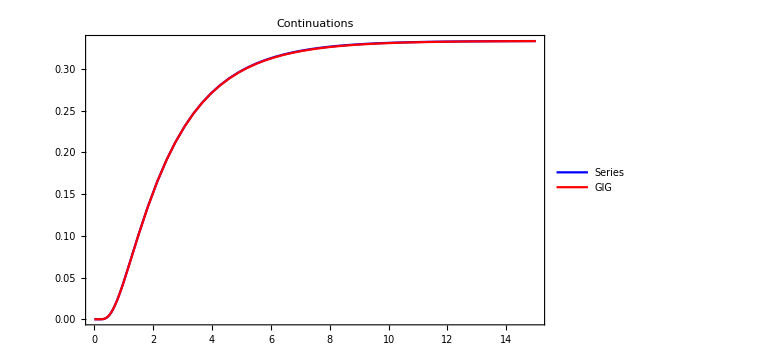
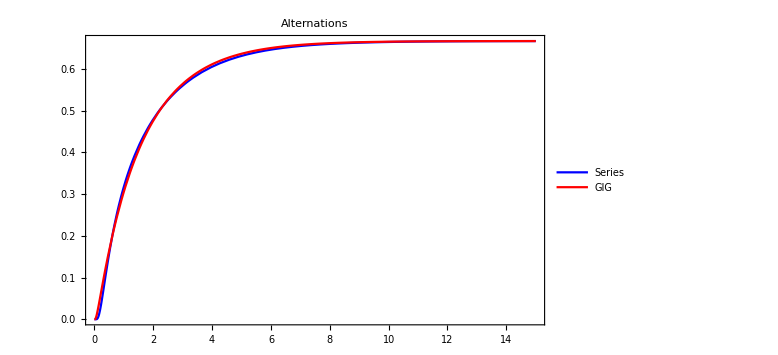

```mathematica
Grid[{{Plot[
{+Pt[-1,1,100,0.01,0.25,0.01,0,t(0.25)(0.01/100 1/0.01)^2],
((2 0.25)/(1+2 0.25))CDF[InverseGaussianDistribution[1.93,3.45,0.23],t]},
{t,0,15},Frame->True,PlotRange->All,ImageSize->Large,
PlotStyle->{Blue,Red},PlotLabel->"Continuations",PlotLegends->{"Series", "GIG"}]},
{Plot[
{+Pt[-1,-1,100,0.01,0.25,0.01,0,t(0.25)(0.01/100 1/0.01)^2],
(1/(1+2 0.25))CDF[InverseGaussianDistribution[0.35,0.14,0.8],t]},
{t,0,15},Frame->True,PlotRange->All,ImageSize->Large,
PlotStyle->{Blue,Red},PlotLabel->"Alternations",PlotLegends->{"Series", "GIG"}]}}]
```

General::munfl: Exp[-5629.37] is too small to represent as a normalized machine number; precision may be lost.

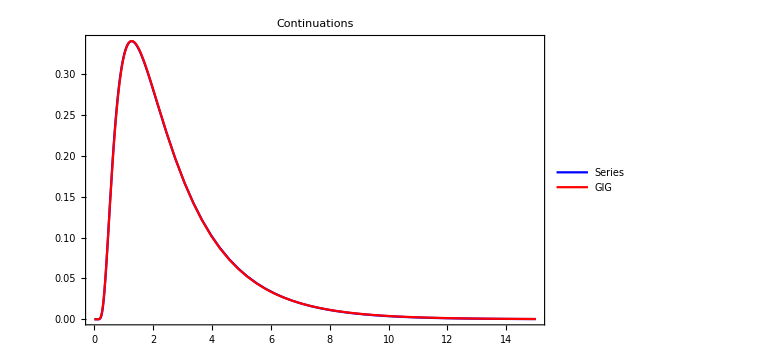
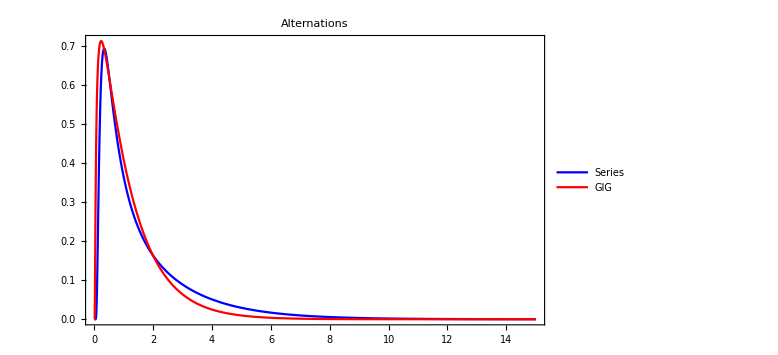
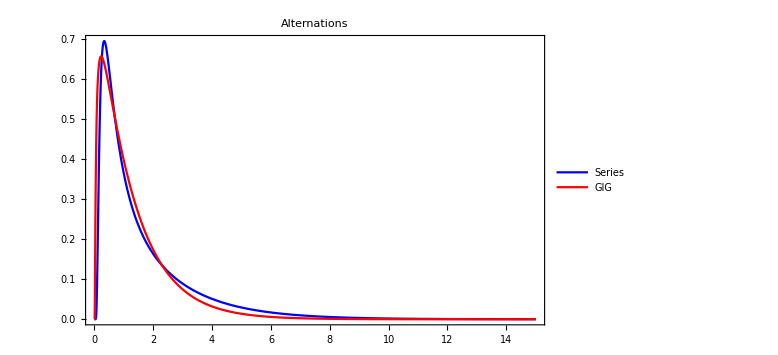

```mathematica
Grid[{{Plot[
{+(0.25)(0.01/100 1/0.01)^2 dPt[-1,1,100,0.01,0.25,0.01,0,t(0.25)(0.01/100 1/0.01)^2],
PDF[InverseGaussianDistribution[1.93,3.45,0.23],t]},
{t,0,15},Frame->True,PlotRange->All,ImageSize->Large,
PlotStyle->{Blue,Red},PlotLabel->"Continuations",PlotLegends->{"Series", "GIG"}]},
{Plot[
{+(0.25)(0.01/100 1/0.01)^2 dPt[-1,-1,100,0.01,0.25,0.01,0,t(0.25)(0.01/100 1/0.01)^2],
PDF[InverseGaussianDistribution[0.23,0.1,1],t]},
{t,0,15},Frame->True,PlotRange->All,ImageSize->Large,
PlotStyle->{Blue,Red},PlotLabel->"Alternations",PlotLegends->{"Series", "GIG"}]},
{Plot[
{+(0.25)(0.01/100 1/0.01)^2 dPt[-1,-1,100,0.01,0.25,0.01,0,t(0.25)(0.01/100 1/0.01)^2],
PDF[InverseGaussianDistribution[0.23,0.09,1],t]},
{t,0,15},Frame->True,PlotRange->All,ImageSize->Large,
PlotStyle->{Blue,Red},PlotLabel->"Alternations",PlotLegends->{"Series", "GIG"}]}}]
```

```mathematica
Plot[Quantile[InverseGaussianDistribution[0.23,3,θ],q],{θ,{-1,1,3}}]//Evaluate,{q,0.01,0.99},Filling->Axis,Frame->True,PlotLegends->{-1,1,3}]
```

Greater::nord: Invalid comparison with -1.05757×10^30-1.72714×10^46 ⅈ attempted.

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {3.19041×10^-9}. Try perturbing the initial point(s).

Greater::nord: Invalid comparison with -1.26253×10^30-2.06187×10^46 ⅈ attempted.

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {6.69101×10^-9}. Try perturbing the initial point(s).

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{10,4.1167,6.88313,-1.56293,4.11702,6.88395,-1.56308,0.0025538,4.44849×10^-6,0.522783,0.00437363,0.0000170857,0.676979}

{20,2.78736,5.32731,-0.374398,2.78754,5.32796,-0.374492,0.00476594,0.0000176556,0.740951,0.00327252,0.0000100767,0.894488}

Greater::nord: Invalid comparison with -19.5529-3.19323×10^17 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {2.59713×10^-7}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{30,2.03764,3.03061,-0.0718535,2.03777,3.03099,-0.071902,0.0064416,0.0000339036,0.650461,0.00441425,0.0000203341,0.839254}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

{40,1.69496,2.41709,0.380068,1.69506,2.41739,0.380055,0.004602,0.0000183476,0.755955,0.009269,0.0000777391,0.796031}

{50,1.97919,3.06203,0.124224,1.97931,3.06241,0.124186,0.00452634,0.0000195536,0.834076,0.00375498,0.0000137329,0.841575}

{60,2.10741,3.29706,-0.0798423,2.10754,3.29747,-0.0798913,0.00295208,9.25644×10^-6,0.84806,0.00799833,0.0000618294,0.796582}

{70,2.27693,3.80322,-0.230742,2.27708,3.8037,-0.230809,0.00422545,0.0000183925,0.832526,0.0103667,0.000108113,0.815648}

{80,2.00932,3.13733,0.0917677,2.00945,3.13772,0.0917249,0.00367426,0.0000150823,0.968327,0.0114145,0.000124169,0.816561}

{90,1.71526,2.58235,0.373013,1.71536,2.58267,0.372992,0.00632611,0.0000392345,0.839086,0.00273302,5.76609×10^-6,0.66622}

{100,1.59924,2.25032,0.483211,1.59933,2.25061,0.483199,0.00693729,0.0000457316,0.824118,0.0036252,0.000012942,0.850901}

10 | 4.1167 | 6.88313 | -1.56293 | 4.11702 | 6.88395 | -1.56308 | 0.0025538 | 4.44849×10^-6 | 0.522783 | 0.00437363 | 0.0000170857 | 0.676979
20 | 2.78736 | 5.32731 | -0.374398 | 2.78754 | 5.32796 | -0.374492 | 0.00476594 | 0.0000176556 | 0.740951 | 0.00327252 | 0.0000100767 | 0.894488
30 | 2.03764 | 3.03061 | -0.0718535 | 2.03777 | 3.03099 | -0.071902 | 0.0064416 | 0.0000339036 | 0.650461 | 0.00441425 | 0.0000203341 | 0.839254
40 | 1.69496 | 2.41709 | 0.380068 | 1.69506 | 2.41739 | 0.380055 | 0.004602 | 0.0000183476 | 0.755955 | 0.009269 | 0.0000777391 | 0.796031
50 | 1.97919 | 3.06203 | 0.124224 | 1.97931 | 3.06241 | 0.124186 | 0.00452634 | 0.0000195536 | 0.834076 | 0.00375498 | 0.0000137329 | 0.841575
60 | 2.10741 | 3.29706 | -0.0798423 | 2.10754 | 3.29747 | -0.0798913 | 0.00295208 | 9.25644×10^-6 | 0.84806 | 0.00799833 | 0.0000618294 | 0.796582
70 | 2.27693 | 3.80322 | -0.230742 | 2.27708 | 3.8037 | -0.230809 | 0.00422545 | 0.0000183925 | 0.832526 | 0.0103667 | 0.000108113 | 0.815648
80 | 2.00932 | 3.13733 | 0.0917677 | 2.00945 | 3.13772 | 0.0917249 | 0.00367426 | 0.0000150823 | 0.968327 | 0.0114145 | 0.000124169 | 0.816561
90 | 1.71526 | 2.58235 | 0.373013 | 1.71536 | 2.58267 | 0.372992 | 0.00632611 | 0.0000392345 | 0.839086 | 0.00273302 | 5.76609×10^-6 | 0.66622
100 | 1.59924 | 2.25032 | 0.483211 | 1.59933 | 2.25061 | 0.483199 | 0.00693729 | 0.0000457316 | 0.824118 | 0.0036252 | 0.000012942 | 0.850901

```mathematica
Ptk[sud_,ud_,s0_,α_,η_,σ_,μ_,t_,k_:1]:=Module[{ω,x0,b1,b2,yn,zn,n=0,ans=0,ϵ=10^-10,pn=1},
If[t==0,0,
ω=μ-1/2 σ^2;
x0=Log[s0+sud(1/2-η)α];
b1=Log[s0+ud(1/2+η+(k-1))α];
b2=Log[s0-ud(1/2+η)α];
While[pn>ϵ,
n++;
yn=+ud*(2*(n-1)*b2-(2n-1)*b1+x0);
zn=+ud*(2*n*b2-(2n-1)*b1-x0);
pn=
(ⅇ^(ω/σ^2 yn)ncdf[(yn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 yn)ncdf[(yn-ω t)/(σ √t)])-
(ⅇ^(ω/σ^2 zn)ncdf[(zn+ω t)/(σ √t)]+ⅇ^(-ω/σ^2 zn)ncdf[(zn-ω t)/(σ √t)]);
ans+=pn;]];
ⅇ^(ω/σ^2(b1-x0))ans];
```

## Four ps - multinomial

```mathematica
multlikel[pw_,x_]:=Factorial[Total[x]]/Apply[Times,Map[Factorial,x]] Apply[Times,MapThread[Power,{pw,x}]];
```

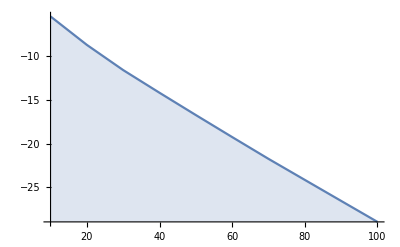

```mathematica
DiscretePlot[Log[Max[Map[multlikel[{0.3,0.3,0.1,0.1},#]&,IntegerPartitions[n,{4}]]]],{n,{10,20,30,40,50,60,70,80,90,100}},Joined->True,PlotRange->All]
```

```mathematica
Table[{n,Log[Max[Map[multlikel[{0.3,0.3,0.1,0.1},#]&,IntegerPartitions[n,{4}]]]]},{n,10,100,10}]
```

{{10,-5.48865},{20,-8.73379},{30,-11.6106},{40,-14.1979},{50,-16.7425},{60,-19.2544},{70,-21.7411},{80,-24.1422},{90,-26.5407},{100,-28.9354}}

```mathematica
Fit[Table[{n,Log[Max[Map[multlikel[{0.3,0.3,0.1,0.1},#]&,IntegerPartitions[n,{4}]]]]},{n,10,100,10}],{1,x},x]
```

-3.6231-0.256648 x

```mathematica
Exp[4+0.25 200]
```

2.83075×10^23

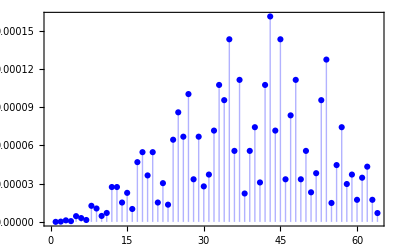

```mathematica
ListPlot[Map[multlikel[{0.3,0.3,0.1,0.1},#]&,IntegerPartitions[20,{4}]],PlotRange->All,PlotStyle->Blue,Filling->Axis,Frame->True]
```

```mathematica
randvec=Map[(#/Total[#])&,RandomReal[1,{10000,4}]];
```

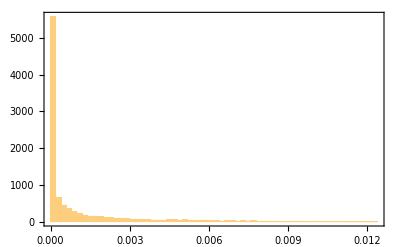

```mathematica
Histogram[Map[multlikel[#,{7,7,3,3}]&,randvec],PlotRange->All,Frame->True,Axes->True,AxesOrigin->{0.005,0}]
```

```mathematica
randveclik=Map[{(#/Total[#]),multlikel[(#/Total[#]),{7,8,5,0}]}&,RandomReal[1,{10000,4}]];
```

```mathematica
Grid[Take[Sort[randveclik,(Last[#1]>Last[#2])&],{1,20}],Frame->All]
```

{0.332061,0.381033,0.286384,0.000522292} | 0.0380154
{0.387678,0.38033,0.229741,0.00225184} | 0.0367926
{0.363267,0.400237,0.23005,0.00644497} | 0.0353372
{0.348542,0.36228,0.284704,0.00447373} | 0.0346022
{0.338891,0.390721,0.262115,0.00827387} | 0.034419
{0.325465,0.364682,0.309271,0.000582652} | 0.0341607
{0.339164,0.40264,0.247064,0.0111312} | 0.032753
{0.325941,0.373978,0.293902,0.00617889} | 0.0327151
{0.30199,0.394849,0.299394,0.00376685} | 0.0324792
{0.372243,0.343252,0.279383,0.00512187} | 0.0324103
{0.322502,0.446829,0.223588,0.00708101} | 0.0321434
{0.313993,0.392707,0.284687,0.00861399} | 0.0317549
{0.363289,0.366892,0.258118,0.0117013} | 0.0313439
{0.34226,0.400269,0.243318,0.0141535} | 0.0308438
{0.352935,0.374226,0.258799,0.0140404} | 0.0303904
{0.320331,0.378128,0.291297,0.0102444} | 0.0302672
{0.403588,0.387837,0.202377,0.00619832} | 0.0302383
{0.394673,0.377882,0.217476,0.00996862} | 0.0300998
{0.382167,0.337786,0.272056,0.00799134} | 0.0300044
{0.306724,0.396858,0.285578,0.0108404} | 0.0297802

```mathematica
Grid[Take[Sort[randveclik,(Last[#1]>Last[#2])&],{1000,1010}],Frame->All]
```

{0.15638,0.405202,0.395722,0.0426959} | 0.00160911
{0.369427,0.516697,0.0804885,0.0333871} | 0.00160788
{0.370128,0.431495,0.107049,0.0913283} | 0.00160387
{0.160143,0.399206,0.391502,0.0491493} | 0.00159879
{0.388234,0.321346,0.160327,0.130094} | 0.00159755
{0.138842,0.533256,0.30079,0.0271116} | 0.00159754
{0.421138,0.192114,0.325814,0.060934} | 0.00159694
{0.50449,0.349816,0.0969794,0.048714} | 0.00159617
{0.214989,0.407233,0.250917,0.126861} | 0.00159331
{0.513964,0.180527,0.272036,0.0334727} | 0.00158853
{0.278001,0.466267,0.14082,0.114913} | 0.00158383

```mathematica
Grid[Take[Sort[randveclik,(Last[#1]>Last[#2])&],{5000,5010}],Frame->All]
```

{0.136637,0.245597,0.349158,0.268608} | 0.000105178
{0.279705,0.128999,0.20497,0.386326} | 0.000105173
{0.253737,0.138997,0.396961,0.210305} | 0.000105071
{0.116958,0.298623,0.286858,0.297561} | 0.000104898
{0.631015,0.159089,0.166218,0.0436779} | 0.000104603
{0.506022,0.252759,0.0185182,0.222701} | 0.000104485
{0.151534,0.215569,0.340123,0.292773} | 0.000104267
{0.153248,0.213678,0.28184,0.351234} | 0.000104193
{0.112348,0.316772,0.283981,0.286899} | 0.000104039
{0.122359,0.391604,0.378578,0.107459} | 0.000103881
{0.489853,0.145153,0.0516917,0.313302} | 0.000103838

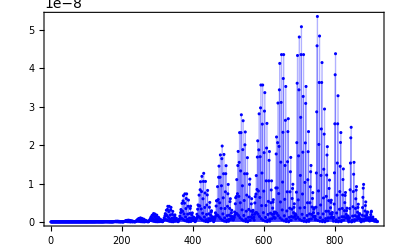

```mathematica
ListPlot[Map[multlikel[{0.3,0.3,0.1,0.1},#]&,IntegerPartitions[50,{4}]],PlotRange->All,PlotStyle->Blue,Filling->Axis,Frame->True]
```

```mathematica
ListPlot[Map[multlikel[{0.3,0.3,0.1,0.1},#]&,IntegerPartitions[200,{4}]],PlotRange->All,PlotStyle->Blue,Filling->Axis,Frame->True]
```

-Graphics-

```mathematica
seed=
{{1,0,0,0},
{0,1,0,0},
{0,0,1,0},
{0,0,0,1}};
```

```mathematica
combine[list1_,list2_]:=Union[Flatten[Outer[Plus,list1,list2,1],1]];
```

```mathematica
combine[seed,seed]
```

{{0,0,0,2},{0,0,1,1},{0,0,2,0},{0,1,0,1},{0,1,1,0},{0,2,0,0},{1,0,0,1},{1,0,1,0},{1,1,0,0},{2,0,0,0}}

```mathematica
combine[%,seed]
```

{{0,0,0,3},{0,0,1,2},{0,0,2,1},{0,0,3,0},{0,1,0,2},{0,1,1,1},{0,1,2,0},{0,2,0,1},{0,2,1,0},{0,3,0,0},{1,0,0,2},{1,0,1,1},{1,0,2,0},{1,1,0,1},{1,1,1,0},{1,2,0,0},{2,0,0,1},{2,0,1,0},{2,1,0,0},{3,0,0,0}}

```mathematica
buildseq[seed_,n_]:=Nest[combine[#,seed]&,seed,n-1];
```

```mathematica
buildseq[seed,1]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
multlikelnet[s0_,α_,η_,σ_,μ_,x_,η_]:=Module[{f4},f4=Freq4[s0,α,η,σ,μ];{σ^2/(α/s0)ArcTanh[(x⟦3⟧-x⟦4⟧)/(2η Total[x])],Simplify[Refine[multlikel[f4,x],σ>0]]}];
```

```mathematica
multlikelalt[s0_,α_,η_,σ_,μ_,x_,η_]:=Module[{f4},f4=Freq4[s0,α,η,σ,μ];{σ^2/(α/s0)ArcTanh[(√Simplify[1-((x⟦1⟧+x⟦2⟧)/Total[x])(1+2η)])/(2η)],Simplify[Refine[multlikel[f4,x],σ>0]]}];
```

```mathematica
freqnet[s0_,α_,η_,σ_,μ_,seed_,n_,η_]:=Module[{f4},f4=Freq4[s0,α,η,σ,μ];GroupBy[Map[{σ^2/(α/s0)ArcTanh[(#⟦3⟧-#⟦4⟧)/(2η Total[#])],Simplify[Refine[multlikel[f4,#],σ>0]]}&,buildseq[seed,n]],First->Last,Total]];
```

```mathematica
freqalt[s0_,α_,η_,σ_,μ_,seed_,n_,η_]:=Module[{f4},f4=Freq4[s0,α,η,σ,μ];GroupBy[Map[{σ^2/(α/s0)ArcTanh[(√Simplify[1-((#⟦1⟧+#⟦2⟧)/Total[#])(1+2η)])/(2η)],Simplify[Refine[multlikel[f4,#],σ>0]]}&,buildseq[seed,n]],First->Last,Total]];
```

```mathematica
freqnetlist[s0_,α_,η_,σ_,μ_,seed_,n_,η_]:=Sort[Map[Apply[List,#]&,Normal[freqnet[s0,α,η,σ,μ,seed,n,η]]]];
```

```mathematica
(* freqnet[pw_,seed_,n_,η_]:=GroupBy[Map[multlikelnet[pw,#,η]&,buildseq[seed,n]],First->Last,Total]; *)
```

```mathematica
freqnet[s0,α,η,σ,0,seed,1,η]
```

<|0→2/(4+8 η),(s0 σ^2 ArcTanh[1/(2 η)])/α→(1+4 η)/(4+8 η),-(s0 σ^2 ArcTanh[1/(2 η)])/α→(1+4 η)/(4+8 η)|>

```mathematica
freqnet[s0,α,η,σ,0,seed,2,η]
```

<|-(s0 σ^2 ArcTanh[1/(2 η)])/α→(1+4 η)^2/(16 (1+2 η)^2),0→1/(4 (1+2 η)^2)+(1+4 η)^2/(8 (1+2 η)^2),(s0 σ^2 ArcTanh[1/(2 η)])/α→(1+4 η)^2/(16 (1+2 η)^2),-(s0 σ^2 ArcTanh[1/(4 η)])/α→(1+4 η)/(4 (1+2 η)^2),(s0 σ^2 ArcTanh[1/(4 η)])/α→(1+4 η)/(4 (1+2 η)^2)|>

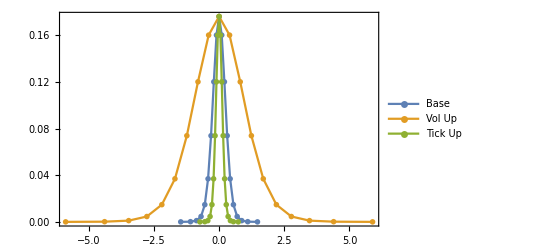

```mathematica
ListPlot[{
freqnetlist[100,0.01,1/2,0.01,0,seed,10,1/2],
freqnetlist[100,0.01,1/2,0.02,0,seed,10,1/2],
freqnetlist[100,0.02,1/2,0.01,0,seed,10,1/2]},
Frame->True,PlotRange->All,
Filling->None,Joined->True,PlotMarkers->"OpenMarkers",
PlotLegends->{"Base","Vol Up","Tick Up"}]
```

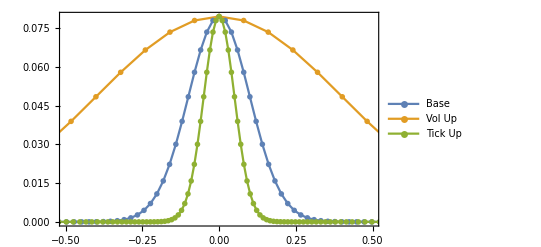

```mathematica
ListPlot[{
freqnetlist[100,0.01,1/2,0.01,0,seed,50,1/2],
freqnetlist[100,0.01,1/2,0.02,0,seed,50,1/2],
freqnetlist[100,0.02,1/2,0.01,0,seed,50,1/2]},
Frame->True,PlotRange->{{-0.5,+0.5},All},Filling->None,Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->{"Base","Vol Up","Tick Up"}]
```

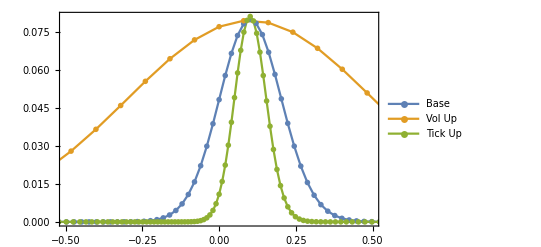

```mathematica
ListPlot[{
freqnetlist[100,0.01,1/2,0.01,0.10,seed,50,1/2],
freqnetlist[100,0.01,1/2,0.02,0.10,seed,50,1/2],
freqnetlist[100,0.02,1/2,0.01,0.10,seed,50,1/2]},
Frame->True,PlotRange->{{-0.5,+0.5},All},Filling->None,Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->{"Base","Vol Up","Tick Up"}]
```

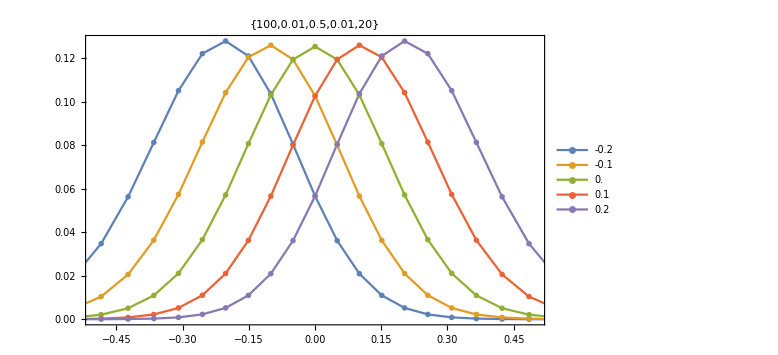

```mathematica
With[{s0=100,α=0.01,η=0.5,σ=0.01,μrng=Range[-0.20,0.20,0.10],n=20},
ListPlot[{
freqnetlist[s0,α,η,σ,μrng⟦1⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦2⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦3⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦4⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦5⟧,seed,n,η]},
Frame->True,PlotRange->{{-0.5,+0.5},All},Filling->None,ImageSize->Large,
Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->μrng,
PlotLabel->{s0,α,η,σ,n}]]
```

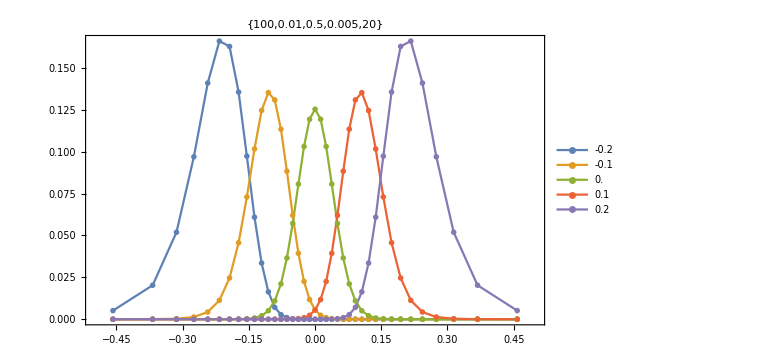

```mathematica
With[{s0=100,α=0.01,η=0.5,σ=0.005,μrng=Range[-0.20,0.20,0.10],n=20},
ListPlot[{
freqnetlist[s0,α,η,σ,μrng⟦1⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦2⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦3⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦4⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦5⟧,seed,n,η]},
Frame->True,PlotRange->{{-0.5,+0.5},All},Filling->None,ImageSize->Large,
Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->μrng,
PlotLabel->{s0,α,η,σ,n}]]
```

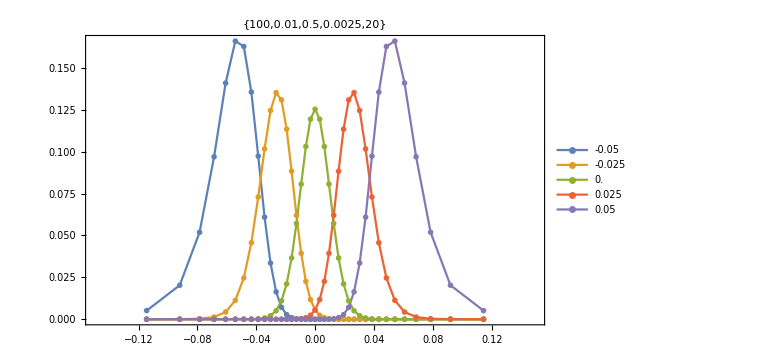

```mathematica
With[{s0=100,α=0.01,η=0.5,σ=0.0025,μrng=Range[-0.05,0.05,0.025],n=20},
ListPlot[{
freqnetlist[s0,α,η,σ,μrng⟦1⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦2⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦3⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦4⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦5⟧,seed,n,η]},
Frame->True,PlotRange->{{-0.15,+0.15},All},Filling->None,ImageSize->Large,
Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->μrng,
PlotLabel->{s0,α,η,σ,n}]]
```

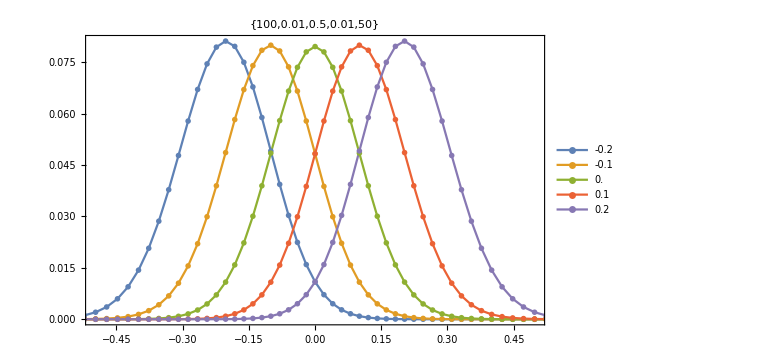

```mathematica
With[{s0=100,α=0.01,η=0.5,σ=0.01,μrng=Range[-0.20,0.20,0.10],n=50},
ListPlot[{
freqnetlist[s0,α,η,σ,μrng⟦1⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦2⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦3⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦4⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦5⟧,seed,n,η]},
Frame->True,PlotRange->{{-0.5,+0.5},All},Filling->None,ImageSize->Large,
Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->μrng,
PlotLabel->{s0,α,η,σ,n}]]
```

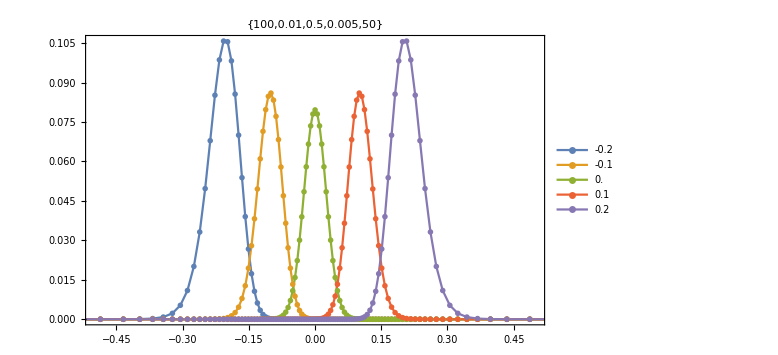

```mathematica
With[{s0=100,α=0.01,η=0.5,σ=0.005,μrng=Range[-0.20,0.20,0.10],n=50},
ListPlot[{
freqnetlist[s0,α,η,σ,μrng⟦1⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦2⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦3⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦4⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦5⟧,seed,n,η]},
Frame->True,PlotRange->{{-0.5,+0.5},All},Filling->None,ImageSize->Large,
Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->μrng,
PlotLabel->{s0,α,η,σ,n}]]
```

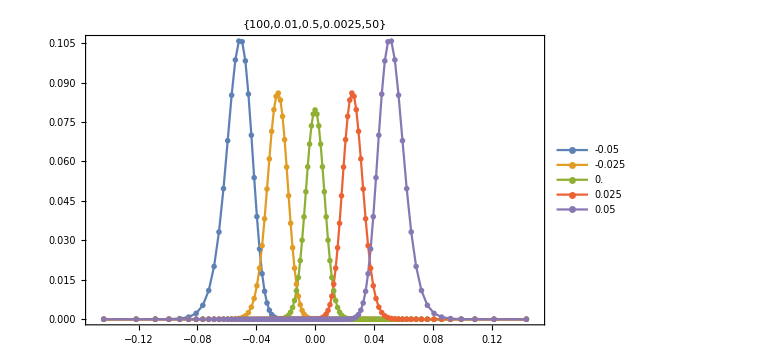

```mathematica
With[{s0=100,α=0.01,η=0.5,σ=0.0025,μrng=Range[-0.05,0.05,0.025],n=50},
ListPlot[{
freqnetlist[s0,α,η,σ,μrng⟦1⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦2⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦3⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦4⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦5⟧,seed,n,η]},
Frame->True,PlotRange->{{-0.15,+0.15},All},Filling->None,ImageSize->Large,
Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->μrng,
PlotLabel->{s0,α,η,σ,n}]]
```

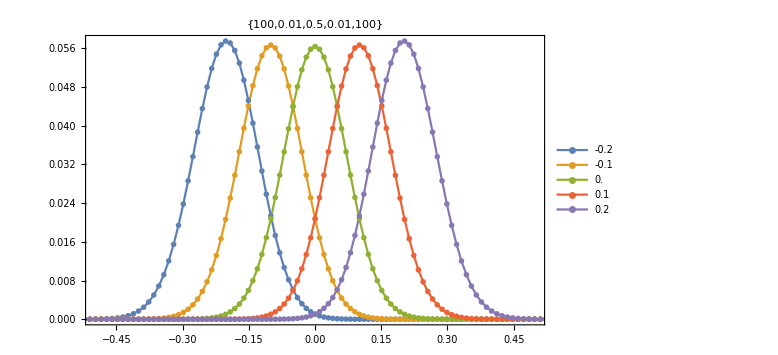

```mathematica
With[{s0=100,α=0.01,η=0.5,σ=0.01,μrng=Range[-0.20,0.20,0.10],n=100},
ListPlot[{
freqnetlist[s0,α,η,σ,μrng⟦1⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦2⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦3⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦4⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦5⟧,seed,n,η]},
Frame->True,PlotRange->{{-0.5,+0.5},All},Filling->None,ImageSize->Large,
Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->μrng,
PlotLabel->{s0,α,η,σ,n}]]
```

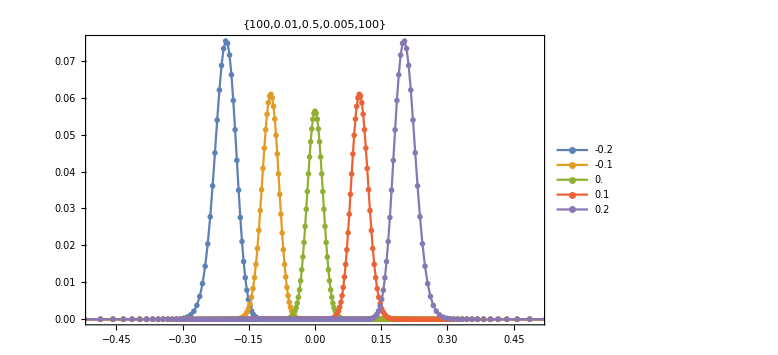

```mathematica
With[{s0=100,α=0.01,η=0.5,σ=0.005,μrng=Range[-0.20,0.20,0.10],n=100},
ListPlot[{
freqnetlist[s0,α,η,σ,μrng⟦1⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦2⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦3⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦4⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦5⟧,seed,n,η]},
Frame->True,PlotRange->{{-0.5,+0.5},All},Filling->None,ImageSize->Large,
Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->μrng,
PlotLabel->{s0,α,η,σ,n}]]
```

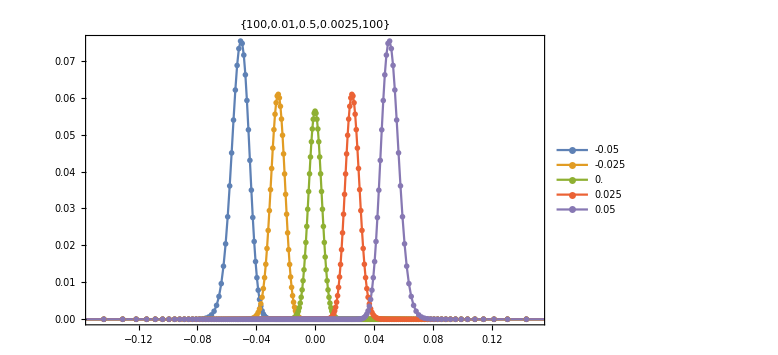

```mathematica
With[{s0=100,α=0.01,η=0.5,σ=0.0025,μrng=Range[-0.05,0.05,0.025],n=100},
ListPlot[{
freqnetlist[s0,α,η,σ,μrng⟦1⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦2⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦3⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦4⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦5⟧,seed,n,η]},
Frame->True,PlotRange->{{-0.15,+0.15},All},Filling->None,ImageSize->Large,
Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->μrng,
PlotLabel->{s0,α,η,σ,n}]]
```

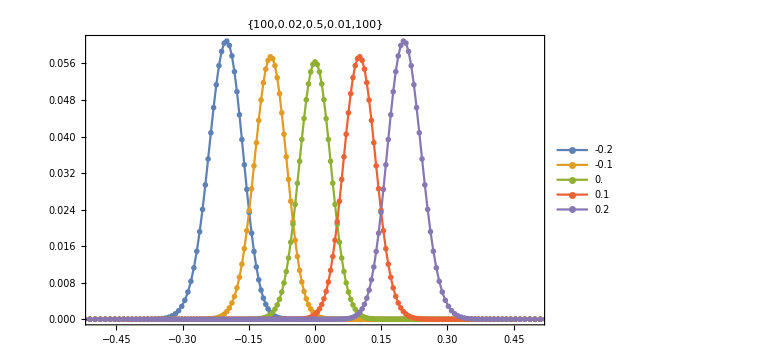

```mathematica
With[{s0=100,α=0.02,η=0.5,σ=0.01,μrng=Range[-0.20,0.20,0.10],n=100},
ListPlot[{
freqnetlist[s0,α,η,σ,μrng⟦1⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦2⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦3⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦4⟧,seed,n,η],
freqnetlist[s0,α,η,σ,μrng⟦5⟧,seed,n,η]},
Frame->True,PlotRange->{{-0.5,+0.5},All},Filling->None,ImageSize->Large,
Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->μrng,
PlotLabel->{s0,α,η,σ,n}]]
```

## Simulation

```mathematica
?Ptinf
```

```mathematica
init={s0,α,η,σ,μ}
```

take init 
draw 2 random numbers
calc Pinf up and down (average on 1 st trade, don't have sud)
choose up or down with r1
now with sud and ud use r2 to choose t
send trade (s0 +- alpha) and ud => next sud

```mathematica
{sud,ud,s0,α,η,σ,μ}
```

```mathematica
Ptinf[
```